```mathematica
(* older Noble fits *)
```

```mathematica
ntjnet=3.464
noblejnetfit1=(-ntjnet+3.13+(horvar-0.061)*(3.08-3.13)/(0.1-0.061))/ntjnet
noblejnetfit2=(-ntjnet+3.13+(horvar-0.061)^2*(3.08-3.13)/(0.1-0.061))/ntjnet
```

3.464

0.288684 (-0.334-1.28205 (-0.061+horvar))

0.288684 (-0.334-1.28205 (-0.061+horvar)^2)

```mathematica
num=7
hor={0.061,0.085,0.1,0.091,0.17,0.13,0.14}
jnet=(-ntjnet+{3.13,3.07,3.08,3.10,2.93,3.21,3.06})/ntjnet
allpoints=Table[{hor[[i]],jnet[[i]]},{i,1,num}]
```

7

{0.061,0.085,0.1,0.091,0.17,0.13,0.14}

{-0.0964203,-0.113741,-0.110855,-0.105081,-0.154157,-0.0733256,-0.116628}

{{0.061,-0.0964203},{0.085,-0.113741},{0.1,-0.110855},{0.091,-0.105081},{0.17,-0.154157},{0.13,-0.0733256},{0.14,-0.116628}}

```mathematica
num=6
hor={0.061,0.085,0.1,0.091,0.17,0.14}
ntjnet=3.464
jnet=(-ntjnet+{3.13,3.07,3.08,3.10,2.93,3.06})/ntjnet
jnetvshor=Table[{hor[[i]],jnet[[i]]},{i,1,num}]
allpoints=Table[{hor[[i]],jnet[[i]]},{i,1,num}]
```

6

{0.061,0.085,0.1,0.091,0.17,0.14}

3.464

{-0.0964203,-0.113741,-0.110855,-0.105081,-0.154157,-0.116628}

{{0.061,-0.0964203},{0.085,-0.113741},{0.1,-0.110855},{0.091,-0.105081},{0.17,-0.154157},{0.14,-0.116628}}

{{0.061,-0.0964203},{0.085,-0.113741},{0.1,-0.110855},{0.091,-0.105081},{0.17,-0.154157},{0.14,-0.116628}}

```mathematica
(* older penna fits *)
```

```mathematica
(* penna 2h/r *)
num=4
hor={0.064,0.12,0.18,0.35}
jnet=(-ntjnet+{3.363,3.138,2.774,2.309})/ntjnet
jnetvshor=Table[{hor[[i]],jnet[[i]]},{i,1,num}]
allpoints=Table[{hor[[i]],jnet[[i]]},{i,1,num}]
```

4

{0.064,0.12,0.18,0.35}

{-0.029157,-0.0941109,-0.199192,-0.33343}

{{0.064,-0.029157},{0.12,-0.0941109},{0.18,-0.199192},{0.35,-0.33343}}

{{0.064,-0.029157},{0.12,-0.0941109},{0.18,-0.199192},{0.35,-0.33343}}

```mathematica
(* penna all angles *)
num=4
hor={0.064,0.12,0.18,0.35}
jnet=(-ntjnet+{3.266,2.908,2.465,2.128})/ntjnet
jnetvshor=Table[{hor[[i]],jnet[[i]]},{i,1,num}]
allpoints=Table[{hor[[i]],jnet[[i]]},{i,1,num}]
```

4

{0.064,0.12,0.18,0.35}

{-0.0571594,-0.160508,-0.288395,-0.385681}

{{0.064,-0.0571594},{0.12,-0.160508},{0.18,-0.288395},{0.35,-0.385681}}

{{0.064,-0.0571594},{0.12,-0.160508},{0.18,-0.288395},{0.35,-0.385681}}

```mathematica
(* old noble or penna fits*)
```

```mathematica
model1=(a+b*horvar)
fitlinear=FindFit[jnetvshor,a+b*horvar,{a,b},horvar]
noblejnetfit1=model1//.fitlinear
model2=a+b*horvar+c*horvar^2
fitpara=FindFit[jnetvshor,model2,{a,b,c},horvar]
noblejnetfit2=(a+b*horvar+c*horvar^2)//.fitpara
```

a+b horvar

{a→-0.0261944,b→-1.10219}

-0.0261944-1.10219 horvar

a+b horvar+c horvar^2

{a→0.128154,b→-3.09043,c→4.62644}

0.128154-3.09043 horvar+4.62644 horvar^2

```mathematica
Solve[noblejnetfit1==0,horvar]
Solve[noblejnetfit2==0,horvar]
```

{{horvar→-0.0237658}}

{{horvar→0.0444222},{horvar→0.623571}}

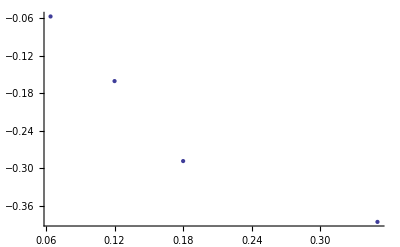

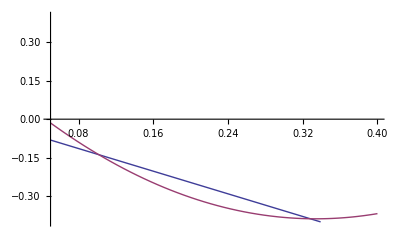

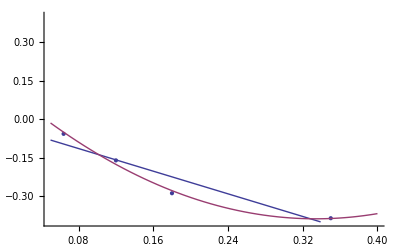

```mathematica
p1=ListPlot[allpoints]
(*p2=Plot[{ntjnet,noblejnetfit1,noblejnetfit2},{horvar,0.05,0.2},PlotRange->{2.8,3.3}]*)
p2=Plot[{noblejnetfit1,noblejnetfit2},{horvar,0.05,0.4},PlotRange->{-0.4,0.4}]
Show[{p1,p2},PlotRange->{-0.4,0.4}]
```

Function[{horvar},-0.0261944-1.10219 horvar]

{0.0395755,-0.00205047,-0.0638057,0.0262807}

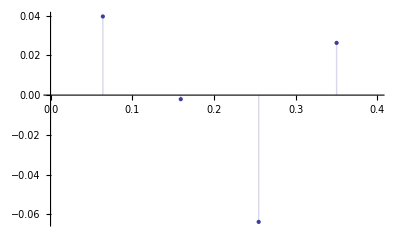

0.260952

0.024266

2.4266

```mathematica
modelf=Function[{horvar},Evaluate[model1/.fitlinear]]
{tl,yl}=Transpose[jnetvshor];
residuals=yl-Map[modelf,tl]
ListPlot[residuals,Filling->Axis,DataRange->{Min[tl],Max[tl]},PlotRange->{{0,0.4},All}]
sumit=(Sum[yl[[i]]^2,{i,1,num}])
error=(residuals.residuals)/sumit
error*100
```

Function[{horvar},0.128154-3.09043 horvar+4.62644 horvar^2]

{-0.00647593,0.0155685,-0.0101685,0.0010759}

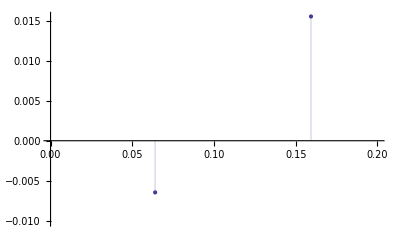

0.260952

0.00149021

0.149021

```mathematica
modelf2=Function[{horvar},Evaluate[model2/.fitpara]]
{tl2,yl2}=Transpose[jnetvshor];
residuals2=yl2-Map[modelf2,tl2]
ListPlot[residuals2,Filling->Axis,DataRange->{Min[tl2],Max[tl2]},PlotRange->{{0,0.2},All}]
(* Dimensions[residuals2][[1]] *)
sumit2=(Sum[yl2[[i]]^2,{i,1,num}])
error2=(residuals2.residuals2)/sumit2
error2*100
```

```mathematica
(* NEW TYPE OF FITS *)
```

```mathematica
data = Import["ExampleData/lubricant.tsv","TSV","HeaderLines"->7];
model=Subscript[θ, 1]/(Subscript[θ, 2]+Subscript[x, 1])+Subscript[θ, 3] Subscript[x, 2]+Subscript[θ, 4] Subscript[x, 2]^2+Subscript[θ, 5] Subscript[x, 2]^3+(Subscript[θ, 6]+Subscript[θ, 7] Subscript[x, 2]^2)Subscript[x, 2] Exp[(-Subscript[x, 1])/(Subscript[θ, 8]+Subscript[θ, 9] Subscript[x, 2]^2)];
sdata=data;
sdata[[All,2]]*=0.001;
fit=FindFit[sdata,model,{Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3],Subscript[θ, 4],Subscript[θ, 5],Subscript[θ, 6],Subscript[θ, 7],Subscript[θ, 8],Subscript[θ, 9]},{Subscript[x, 1],Subscript[x, 2]}]
Show[{Plot3D[Evaluate[model/.fit],{Subscript[x, 1],0,100},{Subscript[x, 2],0,8}],Graphics3D[{Red,PointSize[.025],Map[Point,sdata]}]}]
```

{θ_1→1054.86,θ_2→206.611,θ_3→1.45998,θ_4→-0.259549,θ_5→0.0225532,θ_6→0.401797,θ_7→0.0352675,θ_8→57.4343,θ_9→-0.475994}

-Graphics3D-

```mathematica
(*lu98=lu//.{a->0.98}
lu7=lu//.{a->0.7}
lu9=lu//.{a->0.9}
lu0=lu//.{a->0.0}
lulist={lu0,lu7,lu9,lu98}
*)
jnt={3.4641016151377553,2.5865003262277386,2.099784756123846,1.682667836096026}
```

{3.4641,2.5865,2.09978,1.68267}

```mathematica
(*{da//.{a->0.},da//.{a->0.7},da//.{a->0.9},da//.{a->0.98}}*)
dant={3.4641016151377553,1.3315469450809574,0.580140141713881,0.1810530900827383}
dant4=Table[dant[[1+Mod[ii-1,4]]],{ii,1,16}]
```

{3.4641,1.33155,0.58014,0.181053}

{3.4641,1.33155,0.58014,0.181053,3.4641,1.33155,0.58014,0.181053,3.4641,1.33155,0.58014,0.181053,3.4641,1.33155,0.58014,0.181053}

```mathematica
thickness1strev={.064,0.065,0.054,0.059,0.12,0.09,0.13,0.1,0.18,0.16,0.21,0.18,0.35,0.34,0.34,0.30}
thickness={0.064,0.065,0.054,0.059,0.12,0.09,0.13,0.099,0.18,0.16,0.21,0.18,0.350,0.34,0.341,0.307}
Dimensions[thickness]
spins={0,0.7,0.9,0.98,0,0.7,0.9,0.98,0,0.7,0.9,0.98,0,0.7,0.9,0.98}
Dimensions[spins]
```

{0.064,0.065,0.054,0.059,0.12,0.09,0.13,0.1,0.18,0.16,0.21,0.18,0.35,0.34,0.34,0.3}

{0.064,0.065,0.054,0.059,0.12,0.09,0.13,0.099,0.18,0.16,0.21,0.18,0.35,0.34,0.341,0.307}

{16}

{0,0.7,0.9,0.98,0,0.7,0.9,0.98,0,0.7,0.9,0.98,0,0.7,0.9,0.98}

{16}

```mathematica
num=6
hornoble={0.061,0.085,0.1,0.091,0.17,0.14}
ntjnet=3.464
jnet=100*(-ntjnet+{3.13,3.07,3.08,3.10,2.93,3.06})/ntjnet
Djnetnoble=Table[{hornoble[[i]],0,jnet[[i]]},{i,1,num}]

one1strev={3.363,1.220,0.523,0.124,3.138,1.184,0.402,0.085,2.774,1.081,0.309,0.001,2.309,0.557,-0.084,-0.166}
one2ndrevbad={3.363,1.220,0.523,0.124,3.138,1.184,0.402,0.084,2.774,1.081,0.309,-0.134,2.309,0.277,-0.080,-0.205}
one={3.363,1.220,0.523,0.124,3.138,1.184,0.402,0.084,2.774,1.081,0.309,0.001,2.309,0.557,-0.080,-0.205}
dimit=Dimensions[one][[1]]
two=Table[{thickness[[ii]],spins[[ii]],one[[ii]]},{ii,1,dimit}]
adotdata=two;
(*adotdata=Delete[two,{{12},{16}}]*)

oneeffall={0.054,0.093,0.135,0.171,0.053,0.093,0.128,0.197,0.050,0.046,0.085,0.154,-0.004,-0.007,-0.004,-0.014}
oneemathall=1-oneeffall
dimit=Dimensions[oneemathall][[1]]
two=Table[{thickness[[ii]],spins[[ii]],oneemathall[[ii]]},{ii,1,dimit}]
effall=two;

onejall={3.266,2.282,1.860,1.559,2.908,2.344,1.823,1.425,2.465,2.186,1.739,1.411,2.128,1.788,1.530,1.597}
dimit=Dimensions[onejall][[1]]
two=Table[{thickness[[ii]],spins[[ii]],onejall[[ii]]},{ii,1,dimit}]
jall=two;

onespinfit=onejall/(2*oneemathall)
dimit=Dimensions[onespinfit][[1]]
two=Table[{thickness[[ii]],spins[[ii]],onespinfit[[ii]]},{ii,1,dimit}]
spinfit=two;

one1strev={3.266,1.012,0.303,-0.065,2.908,1.074,0.254,-0.136,2.465,0.851,0.092,-0.247,2.128,0.377,-0.284,-0.298}
one2ndrevbad={3.266,1.012,0.303,-0.065,2.908,1.074,0.254,-0.149,2.465,0.851,0.092,-0.599,2.128,0.046,-0.276,-0.390}
one={3.266,1.012,0.303,-0.065,2.908,1.074,0.254,-0.149,2.465,0.851,0.092,-0.247,2.128,0.377,-0.276,-0.390}
dimit=Dimensions[one][[1]]
two=Table[{thickness[[ii]],spins[[ii]],one[[ii]]},{ii,1,dimit}]
adotdataall=two;
(*adotdataall=Delete[two,{{12},{16}}]*)
Dadot=Table[{thickness[[ii]],spins[[ii]],(one[[ii]]-dant4[[ii]])/dant4[[ii]]},{ii,1,dimit}]


one1strev={-2.913,-4.465,-2.762,-2.335,-9.424,-5.447,-7.261,-3.940,-19.916,-6.736,-7.315,-5.650,-33.331,-23.970,-18.362,6.491}
one2ndrevbad={-2.913,-4.465,-2.762,-2.335,-9.424,-5.447,-7.261,-3.393,-19.916,-6.736,-7.315,-8.945,-33.331,-35.349,-17.999,5.987}
one={-2.913-4.465,-2.762,-2.335,-9.424,-5.447,-7.261,-3.393,-19.916,-6.736,-7.315,-5.650,-33.331,-23.970,-17.999,5.987}
dimit=Dimensions[one][[1]]
two=Table[{thickness[[ii]],spins[[ii]],one[[ii]]},{ii,1,dimit}]
Dj=two;
(*Dj=Delete[two,{{12},{16}}]*)

one1strev={-5.717,-11.776,-11.404,-7.348,-16.046,-9.376,-13.164,-15.076,-28.830,-15.499,-17.164,-16.120,-38.572,-30.878,-27.593,-1.104}
one2ndrevbad={-5.717,-11.776,-11.404,-7.348,-16.046,-9.376,-13.164,-15.291,-28.830,-15.499,-17.164,-41.336,-38.572,-44.252,-27.117,-5.105}
one={-5.717,-11.776,-11.404,-7.348,-16.046,-9.376,-13.164,-15.291,-28.830,-15.499,-17.164,-16.120,-38.572,-30.878,-27.117,-5.105}
dimit=Dimensions[one][[1]]
two=Table[{thickness[[ii]],spins[[ii]],one[[ii]]},{ii,1,dimit}]
Djall=two;
(*Djall=Delete[two,{{12},{16}}]*)


one1strev={-3.153,-2.294,-1.213,-0.199,-8.724,-2.409,1.157,0.660,-17.098,-0.425,2.624,11.117,-30.473,-13.549,-4.470,6.137}
one2ndrevbad={-3.153,-2.294,-1.213,-0.199,-8.724,-2.409,1.157,1.200,-17.098,-0.425,2.624,14.875,-30.473,-12.253,-4.832,12.102}
one={-3.153,-2.294,-1.213,-0.199,-8.724,-2.409,1.157,1.200,-17.098,-0.425,2.624,11.117,-30.473,-13.549,-4.832,12.102}
dimit=Dimensions[one][[1]]
two=Table[{thickness[[ii]],spins[[ii]],one[[ii]]},{ii,1,dimit}]
Djin=two;
(*Djin=Delete[two,{{12},{16}}]*)

one1strev={-5.275,-2.933,5.222,6.905,-13.961,-4.988,-1.449,8.824,-25.067,-7.453,-2.001,11.497,-35.919,-20.166,-9.997,-2.996}
one2ndrevbad={-5.275,-2.933,5.222,6.905,-13.961,-4.988,-1.449,11.744,-25.067,-7.453,-2.001,44.632,-35.919,-16.489,-10.977,-1.624}
one={-5.275,-2.933,5.222,6.905,-13.961,-4.988,-1.449,11.744,-25.067,-7.453,-2.001,11.497,-35.919,-20.166,-10.977,-1.624}
dimit=Dimensions[one][[1]]
two=Table[{thickness[[ii]],spins[[ii]],one[[ii]]},{ii,1,dimit}]
Djinall=two;
(*Djinall=Delete[two,{{12},{16}}]*)

Print["upsilon"]
oneold={0.371,0.321,0.181,0.185,0.569,0.268,0.303,0.185,0.705,0.366,0.319,0.265,0.637,0.401,0.316,0.227}
one1strev={0.450,0.393,0.218,0.228,0.871,0.406,0.466,0.278,1.235,0.6310,0.557,0.459,1.182,0.746,0.573,0.404}
one2ndrevbad={0.450,0.393,0.218,0.228,0.871,0.406,0.466,0.254,1.235,0.631,0.557,0.517,1.182,1.341,0.543,0.246}
one={0.450,0.393,0.218,0.228,0.871,0.406,0.466,0.254,1.235,0.631,0.557,0.459,1.182,0.746,0.543,0.246}
dimit=Dimensions[one][[1]]
two=Table[{thickness[[ii]],spins[[ii]],one[[ii]]},{ii,1,dimit}]
upsilon=two;
(*upsilon=Delete[two,{{12},{16}}]*)

Print["upsilonall"]
oneold={0.560,0.710,0.757,0.384,0.688,0.291,0.377,0.580,0.816,0.421,0.463,0.395,0.628,0.432,0.425,0.189}
one1strev={0.863,1.156,1.299,0.626,1.247,0.525,0.735,1.260,1.771,0.923,1.093,0.887,1.331,0.952,0.990,0.374}
one2ndrevbad={0.863,1.156,1.299,0.626,1.247,0.525,0.735,1.349,1.771,0.923,1.093,2.827,1.331,1.994,0.914,0.273}
one={0.863,1.156,1.299,0.626,1.247,0.525,0.735,1.349,1.771,0.923,1.093,0.887,1.331,0.952,0.914,0.273}
dimit=Dimensions[one][[1]]
two=Table[{thickness[[ii]],spins[[ii]],one[[ii]]},{ii,1,dimit}]
upsilonall=two;
(*upsilonall=Delete[two,{{12},{16}}]*)

one1strev={0.035,0.0480,.041,0.069,0.084,0.060,0.068,0.063,0.167,0.050,0.011,0.52,0.000,0.000,0.000,0.000}
one2ndrevbad={0.035,0.048,0.041,0.069,0.084,0.060,0.068,0.062,0.167,0.050,0.011,0.028,0.000,0.000,0.000,0.000}
one={0.035,0.048,0.041,0.069,0.084,0.060,0.068,0.062,0.167,0.050,0.011,0.052,0.000,0.000,0.000,0.000}
dimit=Dimensions[one][[1]]
two=Table[{thickness[[ii]],spins[[ii]],one[[ii]]},{ii,1,dimit}]
lum=Delete[two,{{9},{10},{11},{12},{13},{14},{15},{16}}]

one1strev={0.035,0.040,0.035,0.048,0.087,0.068,0.066,0.077,0.164,0.045,0.012,0.045,0.000,0.000,0.000,0.000}
one2ndrevbad={0.035,0.040,0.035,0.048,0.087,0.068,0.066,0.078,0.164,0.045,0.012,0.028,0.000,0.000,0.000,0.000}
one={0.035,0.040,0.035,0.048,0.087,0.068,0.066,0.078,0.164,0.045,0.012,0.045,0.000,0.000,0.000,0.000}
dimit=Dimensions[one][[1]]
two=Table[{thickness[[ii]],spins[[ii]],one[[ii]]},{ii,1,dimit}]
lumall=Delete[two,{{9},{10},{11},{12},{13},{14},{15},{16}}]

one1strev={-0.829,-2.899,-0.157,3.897,1.470,4.808,9.014,6.471,4.134,52.330,41.922,18.496,104.582,106.384,99.5,99.632}
one2ndrevbad={-0.829,-2.899,-0.157,3.897,1.470,4.808,9.014,8.810,4.134,52.330,41.922,35.943,104.582,96.563,100.582,106.206}
one={-0.829,-2.899,-0.157,3.897,1.470,4.808,9.014,8.810,4.134,52.330,41.922,18.496,104.582,106.384,100.582,106.206}
dimit=Dimensions[one][[1]]
two=Table[{thickness[[ii]],spins[[ii]],one[[ii]]},{ii,1,dimit}]
Deffdata=Delete[two,{{9},{10},{11},{12},{13},{14},{15},{16}}]
(*Deffdata=Delete[two,{{13},{14},{15},{16}}]*)

one1strev={4.723,10.132,13.294,26.735,6.579,10.343,17.577,13.735,12.631,55.244,45.564,34.174,106.180,107.191,101.601,100.467}
one2ndrevbad={4.723,10.132,13.294,26.735,6.579,10.343,17.577,15.950,12.631,55.244,45.564,18.422,106.180,97.155,102.370,105.873}
one={4.723,10.132,13.294,26.735,6.579,10.343,17.577,15.950,12.631,55.244,45.564,34.174,106.180,107.191,102.370,105.873}
dimit=Dimensions[one][[1]]
two=Table[{thickness[[ii]],spins[[ii]],one[[ii]]},{ii,1,dimit}]
Deffdataall=Delete[two,{{9},{10},{11},{12},{13},{14},{15},{16}}]
```

6

{0.061,0.085,0.1,0.091,0.17,0.14}

3.464

{-9.64203,-11.3741,-11.0855,-10.5081,-15.4157,-11.6628}

{{0.061,0,-9.64203},{0.085,0,-11.3741},{0.1,0,-11.0855},{0.091,0,-10.5081},{0.17,0,-15.4157},{0.14,0,-11.6628}}

{3.363,1.22,0.523,0.124,3.138,1.184,0.402,0.085,2.774,1.081,0.309,0.001,2.309,0.557,-0.084,-0.166}

{3.363,1.22,0.523,0.124,3.138,1.184,0.402,0.084,2.774,1.081,0.309,-0.134,2.309,0.277,-0.08,-0.205}

{3.363,1.22,0.523,0.124,3.138,1.184,0.402,0.084,2.774,1.081,0.309,0.001,2.309,0.557,-0.08,-0.205}

16

{{0.064,0,3.363},{0.065,0.7,1.22},{0.054,0.9,0.523},{0.059,0.98,0.124},{0.12,0,3.138},{0.09,0.7,1.184},{0.13,0.9,0.402},{0.099,0.98,0.084},{0.18,0,2.774},{0.16,0.7,1.081},{0.21,0.9,0.309},{0.18,0.98,0.001},{0.35,0,2.309},{0.34,0.7,0.557},{0.341,0.9,-0.08},{0.307,0.98,-0.205}}

{0.054,0.093,0.135,0.171,0.053,0.093,0.128,0.197,0.05,0.046,0.085,0.154,-0.004,-0.007,-0.004,-0.014}

{0.946,0.907,0.865,0.829,0.947,0.907,0.872,0.803,0.95,0.954,0.915,0.846,1.004,1.007,1.004,1.014}

16

{{0.064,0,0.946},{0.065,0.7,0.907},{0.054,0.9,0.865},{0.059,0.98,0.829},{0.12,0,0.947},{0.09,0.7,0.907},{0.13,0.9,0.872},{0.099,0.98,0.803},{0.18,0,0.95},{0.16,0.7,0.954},{0.21,0.9,0.915},{0.18,0.98,0.846},{0.35,0,1.004},{0.34,0.7,1.007},{0.341,0.9,1.004},{0.307,0.98,1.014}}

{3.266,2.282,1.86,1.559,2.908,2.344,1.823,1.425,2.465,2.186,1.739,1.411,2.128,1.788,1.53,1.597}

16

{{0.064,0,3.266},{0.065,0.7,2.282},{0.054,0.9,1.86},{0.059,0.98,1.559},{0.12,0,2.908},{0.09,0.7,2.344},{0.13,0.9,1.823},{0.099,0.98,1.425},{0.18,0,2.465},{0.16,0.7,2.186},{0.21,0.9,1.739},{0.18,0.98,1.411},{0.35,0,2.128},{0.34,0.7,1.788},{0.341,0.9,1.53},{0.307,0.98,1.597}}

{1.72622,1.25799,1.07514,0.94029,1.53537,1.29217,1.0453,0.887298,1.29737,1.1457,0.950273,0.833924,1.05976,0.887786,0.761952,0.787475}

16

{{0.064,0,1.72622},{0.065,0.7,1.25799},{0.054,0.9,1.07514},{0.059,0.98,0.94029},{0.12,0,1.53537},{0.09,0.7,1.29217},{0.13,0.9,1.0453},{0.099,0.98,0.887298},{0.18,0,1.29737},{0.16,0.7,1.1457},{0.21,0.9,0.950273},{0.18,0.98,0.833924},{0.35,0,1.05976},{0.34,0.7,0.887786},{0.341,0.9,0.761952},{0.307,0.98,0.787475}}

{3.266,1.012,0.303,-0.065,2.908,1.074,0.254,-0.136,2.465,0.851,0.092,-0.247,2.128,0.377,-0.284,-0.298}

{3.266,1.012,0.303,-0.065,2.908,1.074,0.254,-0.149,2.465,0.851,0.092,-0.599,2.128,0.046,-0.276,-0.39}

{3.266,1.012,0.303,-0.065,2.908,1.074,0.254,-0.149,2.465,0.851,0.092,-0.247,2.128,0.377,-0.276,-0.39}

16

{{0.064,0,3.266},{0.065,0.7,1.012},{0.054,0.9,0.303},{0.059,0.98,-0.065},{0.12,0,2.908},{0.09,0.7,1.074},{0.13,0.9,0.254},{0.099,0.98,-0.149},{0.18,0,2.465},{0.16,0.7,0.851},{0.21,0.9,0.092},{0.18,0.98,-0.247},{0.35,0,2.128},{0.34,0.7,0.377},{0.341,0.9,-0.276},{0.307,0.98,-0.39}}

{{0.064,0,-0.057187},{0.065,0.7,-0.239982},{0.054,0.9,-0.477712},{0.059,0.98,-1.35901},{0.12,0,-0.160533},{0.09,0.7,-0.193419},{0.13,0.9,-0.562175},{0.099,0.98,-1.82296},{0.18,0,-0.288416},{0.16,0.7,-0.360894},{0.21,0.9,-0.841418},{0.18,0.98,-2.36424},{0.35,0,-0.385699},{0.34,0.7,-0.716871},{0.341,0.9,-1.47575},{0.307,0.98,-3.15406}}

{-2.913,-4.465,-2.762,-2.335,-9.424,-5.447,-7.261,-3.94,-19.916,-6.736,-7.315,-5.65,-33.331,-23.97,-18.362,6.491}

{-2.913,-4.465,-2.762,-2.335,-9.424,-5.447,-7.261,-3.393,-19.916,-6.736,-7.315,-8.945,-33.331,-35.349,-17.999,5.987}

{-7.378,-2.762,-2.335,-9.424,-5.447,-7.261,-3.393,-19.916,-6.736,-7.315,-5.65,-33.331,-23.97,-17.999,5.987}

15

{{0.064,0,-7.378},{0.065,0.7,-2.762},{0.054,0.9,-2.335},{0.059,0.98,-9.424},{0.12,0,-5.447},{0.09,0.7,-7.261},{0.13,0.9,-3.393},{0.099,0.98,-19.916},{0.18,0,-6.736},{0.16,0.7,-7.315},{0.21,0.9,-5.65},{0.18,0.98,-33.331},{0.35,0,-23.97},{0.34,0.7,-17.999},{0.341,0.9,5.987}}

{-5.717,-11.776,-11.404,-7.348,-16.046,-9.376,-13.164,-15.076,-28.83,-15.499,-17.164,-16.12,-38.572,-30.878,-27.593,-1.104}

{-5.717,-11.776,-11.404,-7.348,-16.046,-9.376,-13.164,-15.291,-28.83,-15.499,-17.164,-41.336,-38.572,-44.252,-27.117,-5.105}

{-5.717,-11.776,-11.404,-7.348,-16.046,-9.376,-13.164,-15.291,-28.83,-15.499,-17.164,-16.12,-38.572,-30.878,-27.117,-5.105}

16

{{0.064,0,-5.717},{0.065,0.7,-11.776},{0.054,0.9,-11.404},{0.059,0.98,-7.348},{0.12,0,-16.046},{0.09,0.7,-9.376},{0.13,0.9,-13.164},{0.099,0.98,-15.291},{0.18,0,-28.83},{0.16,0.7,-15.499},{0.21,0.9,-17.164},{0.18,0.98,-16.12},{0.35,0,-38.572},{0.34,0.7,-30.878},{0.341,0.9,-27.117},{0.307,0.98,-5.105}}

{-3.153,-2.294,-1.213,-0.199,-8.724,-2.409,1.157,0.66,-17.098,-0.425,2.624,11.117,-30.473,-13.549,-4.47,6.137}

{-3.153,-2.294,-1.213,-0.199,-8.724,-2.409,1.157,1.2,-17.098,-0.425,2.624,14.875,-30.473,-12.253,-4.832,12.102}

{-3.153,-2.294,-1.213,-0.199,-8.724,-2.409,1.157,1.2,-17.098,-0.425,2.624,11.117,-30.473,-13.549,-4.832,12.102}

16

{{0.064,0,-3.153},{0.065,0.7,-2.294},{0.054,0.9,-1.213},{0.059,0.98,-0.199},{0.12,0,-8.724},{0.09,0.7,-2.409},{0.13,0.9,1.157},{0.099,0.98,1.2},{0.18,0,-17.098},{0.16,0.7,-0.425},{0.21,0.9,2.624},{0.18,0.98,11.117},{0.35,0,-30.473},{0.34,0.7,-13.549},{0.341,0.9,-4.832},{0.307,0.98,12.102}}

{-5.275,-2.933,5.222,6.905,-13.961,-4.988,-1.449,8.824,-25.067,-7.453,-2.001,11.497,-35.919,-20.166,-9.997,-2.996}

{-5.275,-2.933,5.222,6.905,-13.961,-4.988,-1.449,11.744,-25.067,-7.453,-2.001,44.632,-35.919,-16.489,-10.977,-1.624}

{-5.275,-2.933,5.222,6.905,-13.961,-4.988,-1.449,11.744,-25.067,-7.453,-2.001,11.497,-35.919,-20.166,-10.977,-1.624}

16

{{0.064,0,-5.275},{0.065,0.7,-2.933},{0.054,0.9,5.222},{0.059,0.98,6.905},{0.12,0,-13.961},{0.09,0.7,-4.988},{0.13,0.9,-1.449},{0.099,0.98,11.744},{0.18,0,-25.067},{0.16,0.7,-7.453},{0.21,0.9,-2.001},{0.18,0.98,11.497},{0.35,0,-35.919},{0.34,0.7,-20.166},{0.341,0.9,-10.977},{0.307,0.98,-1.624}}

upsilon

{0.371,0.321,0.181,0.185,0.569,0.268,0.303,0.185,0.705,0.366,0.319,0.265,0.637,0.401,0.316,0.227}

{0.45,0.393,0.218,0.228,0.871,0.406,0.466,0.278,1.235,0.631,0.557,0.459,1.182,0.746,0.573,0.404}

{0.45,0.393,0.218,0.228,0.871,0.406,0.466,0.254,1.235,0.631,0.557,0.517,1.182,1.341,0.543,0.246}

{0.45,0.393,0.218,0.228,0.871,0.406,0.466,0.254,1.235,0.631,0.557,0.459,1.182,0.746,0.543,0.246}

16

{{0.064,0,0.45},{0.065,0.7,0.393},{0.054,0.9,0.218},{0.059,0.98,0.228},{0.12,0,0.871},{0.09,0.7,0.406},{0.13,0.9,0.466},{0.099,0.98,0.254},{0.18,0,1.235},{0.16,0.7,0.631},{0.21,0.9,0.557},{0.18,0.98,0.459},{0.35,0,1.182},{0.34,0.7,0.746},{0.341,0.9,0.543},{0.307,0.98,0.246}}

upsilonall

{0.56,0.71,0.757,0.384,0.688,0.291,0.377,0.58,0.816,0.421,0.463,0.395,0.628,0.432,0.425,0.189}

{0.863,1.156,1.299,0.626,1.247,0.525,0.735,1.26,1.771,0.923,1.093,0.887,1.331,0.952,0.99,0.374}

{0.863,1.156,1.299,0.626,1.247,0.525,0.735,1.349,1.771,0.923,1.093,2.827,1.331,1.994,0.914,0.273}

{0.863,1.156,1.299,0.626,1.247,0.525,0.735,1.349,1.771,0.923,1.093,0.887,1.331,0.952,0.914,0.273}

16

{{0.064,0,0.863},{0.065,0.7,1.156},{0.054,0.9,1.299},{0.059,0.98,0.626},{0.12,0,1.247},{0.09,0.7,0.525},{0.13,0.9,0.735},{0.099,0.98,1.349},{0.18,0,1.771},{0.16,0.7,0.923},{0.21,0.9,1.093},{0.18,0.98,0.887},{0.35,0,1.331},{0.34,0.7,0.952},{0.341,0.9,0.914},{0.307,0.98,0.273}}

{0.035,0.048,0.041,0.069,0.084,0.06,0.068,0.063,0.167,0.05,0.011,0.52,0.,0.,0.,0.}

{0.035,0.048,0.041,0.069,0.084,0.06,0.068,0.062,0.167,0.05,0.011,0.028,0.,0.,0.,0.}

{0.035,0.048,0.041,0.069,0.084,0.06,0.068,0.062,0.167,0.05,0.011,0.052,0.,0.,0.,0.}

16

{{0.064,0,0.035},{0.065,0.7,0.048},{0.054,0.9,0.041},{0.059,0.98,0.069},{0.12,0,0.084},{0.09,0.7,0.06},{0.13,0.9,0.068},{0.099,0.98,0.062},{0.18,0,0.167},{0.16,0.7,0.05},{0.21,0.9,0.011},{0.18,0.98,0.052},{0.35,0,0.},{0.34,0.7,0.},{0.341,0.9,0.},{0.307,0.98,0.}}

{{0.064,0,0.035},{0.065,0.7,0.048},{0.054,0.9,0.041},{0.059,0.98,0.069},{0.12,0,0.084},{0.09,0.7,0.06},{0.13,0.9,0.068},{0.099,0.98,0.062}}

{0.035,0.04,0.035,0.048,0.087,0.068,0.066,0.077,0.164,0.045,0.012,0.045,0.,0.,0.,0.}

{0.035,0.04,0.035,0.048,0.087,0.068,0.066,0.078,0.164,0.045,0.012,0.028,0.,0.,0.,0.}

{0.035,0.04,0.035,0.048,0.087,0.068,0.066,0.078,0.164,0.045,0.012,0.045,0.,0.,0.,0.}

16

{{0.064,0,0.035},{0.065,0.7,0.04},{0.054,0.9,0.035},{0.059,0.98,0.048},{0.12,0,0.087},{0.09,0.7,0.068},{0.13,0.9,0.066},{0.099,0.98,0.078},{0.18,0,0.164},{0.16,0.7,0.045},{0.21,0.9,0.012},{0.18,0.98,0.045},{0.35,0,0.},{0.34,0.7,0.},{0.341,0.9,0.},{0.307,0.98,0.}}

{{0.064,0,0.035},{0.065,0.7,0.04},{0.054,0.9,0.035},{0.059,0.98,0.048},{0.12,0,0.087},{0.09,0.7,0.068},{0.13,0.9,0.066},{0.099,0.98,0.078}}

{-0.829,-2.899,-0.157,3.897,1.47,4.808,9.014,6.471,4.134,52.33,41.922,18.496,104.582,106.384,99.5,99.632}

{-0.829,-2.899,-0.157,3.897,1.47,4.808,9.014,8.81,4.134,52.33,41.922,35.943,104.582,96.563,100.582,106.206}

{-0.829,-2.899,-0.157,3.897,1.47,4.808,9.014,8.81,4.134,52.33,41.922,18.496,104.582,106.384,100.582,106.206}

16

{{0.064,0,-0.829},{0.065,0.7,-2.899},{0.054,0.9,-0.157},{0.059,0.98,3.897},{0.12,0,1.47},{0.09,0.7,4.808},{0.13,0.9,9.014},{0.099,0.98,8.81},{0.18,0,4.134},{0.16,0.7,52.33},{0.21,0.9,41.922},{0.18,0.98,18.496},{0.35,0,104.582},{0.34,0.7,106.384},{0.341,0.9,100.582},{0.307,0.98,106.206}}

{{0.064,0,-0.829},{0.065,0.7,-2.899},{0.054,0.9,-0.157},{0.059,0.98,3.897},{0.12,0,1.47},{0.09,0.7,4.808},{0.13,0.9,9.014},{0.099,0.98,8.81}}

{4.723,10.132,13.294,26.735,6.579,10.343,17.577,13.735,12.631,55.244,45.564,34.174,106.18,107.191,101.601,100.467}

{4.723,10.132,13.294,26.735,6.579,10.343,17.577,15.95,12.631,55.244,45.564,18.422,106.18,97.155,102.37,105.873}

{4.723,10.132,13.294,26.735,6.579,10.343,17.577,15.95,12.631,55.244,45.564,34.174,106.18,107.191,102.37,105.873}

16

{{0.064,0,4.723},{0.065,0.7,10.132},{0.054,0.9,13.294},{0.059,0.98,26.735},{0.12,0,6.579},{0.09,0.7,10.343},{0.13,0.9,17.577},{0.099,0.98,15.95},{0.18,0,12.631},{0.16,0.7,55.244},{0.21,0.9,45.564},{0.18,0.98,34.174},{0.35,0,106.18},{0.34,0.7,107.191},{0.341,0.9,102.37},{0.307,0.98,105.873}}

{{0.064,0,4.723},{0.065,0.7,10.132},{0.054,0.9,13.294},{0.059,0.98,26.735},{0.12,0,6.579},{0.09,0.7,10.343},{0.13,0.9,17.577},{0.099,0.98,15.95}}

```mathematica
(* Try to fit *)
```

```mathematica
(*data=Djnetnoble*)
(*DONTUSE data=adotdata*)
(*data=adotdataall*)
(*data=Deffdata*)
(*data=Deffdataall*)
(*data=Dj*)
(*data=Djall*)
(*data=Djin*)
(*data=Djinall*)
(*data=lumall*)
(*data=upsilon*)
data=upsilonall
(*data=spinfit*)
rp=1+Sqrt[1-avar^2]
omegah=avar/(2*rp)
model=a+b*horvar+c*avar
(*model=a+b*horvar+c*horvar^2*)
Print["fit"]
fit=FindFit[data,model,{a,b,c,d},{horvar,avar}]
finalsol=model//.fit
Print["nonlinearmodelfit"]
clevel1=0.682689492137;
clevel2=0.954499736104;
clevel95=.95;
clevel975=0.975;
clevel3=0.997300203937;
clevel4=0.999936657516;
clevel5=0.999999426697;
clevel6=0.999999998027;
nlm=NonlinearModelFit[data,model,{a,b,c,d},{horvar,avar},ConfidenceLevel->clevel95]
nlmint=nlm["ParameterConfidenceIntervals"]
Print["clevel95"];clevel95
nlmtable=nlm["ParameterConfidenceIntervalTable",ConfidenceLevel->clevel95]
Print["clevel975"];clevel975
nlmtable=nlm["ParameterConfidenceIntervalTable",ConfidenceLevel->clevel975]
Print["clevel2"];clevel2
nlmtable=nlm["ParameterConfidenceIntervalTable",ConfidenceLevel->clevel2]
Print["clevel3"];clevel3
nlmtable=nlm["ParameterConfidenceIntervalTable",ConfidenceLevel->clevel3]
Print["clevel4"];clevel4
nlmtable=nlm["ParameterConfidenceIntervalTable",ConfidenceLevel->clevel4]
Print["clevel5"];clevel5
nlmtable=nlm["ParameterConfidenceIntervalTable",ConfidenceLevel->clevel5]
Print["clevel6"];clevel6
nlmtable=nlm["ParameterConfidenceIntervalTable",ConfidenceLevel->clevel6]
nlmvar=nlm["EstimatedVariance"]
{bands90[x_,y_],bands95[x_,y_],bands99[x_,y_],bands999[x_,y_]}=Table[nlm["MeanPredictionBands",ConfidenceLevel->cl],{cl,{.9,.95,.99,.999}}];
Print["Relative difference for each parameter: a + b*horvar + c*avar"]
nlmdiff=Table[Abs[(nlmint[[ii,1]]-nlmint[[ii,2]])]/(Abs[nlmint[[ii,1]]]+Abs[nlmint[[ii,2]]]),{ii,1,3}]
Show[{Plot3D[Evaluate[model/.fit],{horvar,0.03,0.3},{avar,-.1,1}],Graphics3D[{Red,PointSize[.025],Map[Point,data]}]}]
modelf=Function[{horvar,avar},Evaluate[finalsol]]
myhor=Table[data[[i,1]],{i,Dimensions[data][[1]]}]
mya=Table[data[[i,2]],{i,Dimensions[data][[1]]}]
mydata=Table[data[[i,3]],{i,Dimensions[data][[1]]}]
Print["L2 error norm"]
l2errornorm=Sum[(modelf[myhor[[i]],mya[[i]]]-mydata[[i]])^2,{i,1,Dimensions[data][[1]]}]/Sum[mydata[[i]]^2,{i,1,Dimensions[data][[1]]}]
```

{{0.064,0,0.863},{0.065,0.7,1.156},{0.054,0.9,1.299},{0.059,0.98,0.626},{0.12,0,1.247},{0.09,0.7,0.525},{0.13,0.9,0.735},{0.099,0.98,1.349},{0.18,0,1.771},{0.16,0.7,0.923},{0.21,0.9,1.093},{0.18,0.98,0.887},{0.35,0,1.331},{0.34,0.7,0.952},{0.341,0.9,0.914},{0.307,0.98,0.273}}

1+√(1-avar^2)

avar/(2 (1+√(1-avar^2)))

a+avar c+b horvar

fit

{a→1.33562,b→-0.256828,c→-0.457351,d→0.}

1.33562-0.457351 avar-0.256828 horvar

nonlinearmodelfit

FittedModel[1.33562-0.457351 avar-0.256828 horvar]

{{0.835466,1.83577},{-2.10977,1.59612},{-0.958875,0.0441725},{0.,0.}}

clevel95

0.95

| Estimate | Standard Error | Confidence Interval
a | 1.33562 | 0.229552 | {0.835466,1.83577}
b | -0.256828 | 0.850438 | {-2.10977,1.59612}
c | -0.457351 | 0.230182 | {-0.958875,0.0441725}
d | 0. | 0. | {0.,0.}

clevel975

0.975

| Estimate | Standard Error | Confidence Interval
a | 1.33562 | 0.229552 | {0.747956,1.92328}
b | -0.256828 | 0.850438 | {-2.43398,1.92032}
c | -0.457351 | 0.230182 | {-1.04663,0.131923}
d | 0. | 0. | {0.,0.}

clevel2

0.9545

| Estimate | Standard Error | Confidence Interval
a | 1.33562 | 0.229552 | {0.823407,1.84783}
b | -0.256828 | 0.850438 | {-2.15445,1.64079}
c | -0.457351 | 0.230182 | {-0.970968,0.0562652}
d | 0. | 0. | {0.,0.}

clevel3

0.9973

| Estimate | Standard Error | Confidence Interval
a | 1.33562 | 0.229552 | {0.471519,2.19972}
b | -0.256828 | 0.850438 | {-3.45811,2.94445}
c | -0.457351 | 0.230182 | {-1.32382,0.409118}
d | 0. | 0. | {0.,0.}

clevel4

0.999937

| Estimate | Standard Error | Confidence Interval
a | 1.33562 | 0.229552 | {-0.0388966,2.71013}
b | -0.256828 | 0.850438 | {-5.34908,4.83543}
c | -0.457351 | 0.230182 | {-1.83564,0.920934}
d | 0. | 0. | {0.,0.}

clevel5

0.999999

| Estimate | Standard Error | Confidence Interval
a | 1.33562 | 0.229552 | {-0.861664,3.5329}
b | -0.256828 | 0.850438 | {-8.39724,7.88359}
c | -0.457351 | 0.230182 | {-2.66066,1.74596}
d | 0. | 0. | {0.,0.}

clevel6

1.

| Estimate | Standard Error | Confidence Interval
a | 1.33562 | 0.229552 | {-2.31739,4.98863}
b | -0.256828 | 0.850438 | {-13.7904,13.2767}
c | -0.457351 | 0.230182 | {-4.12038,3.20568}
d | 0. | 0. | {0.,0.}

0.126243

Relative difference for each parameter: a + b*horvar + c*avar

{0.374472,1.,1.}

-Graphics3D-

Function[{horvar,avar},1.33562-0.457351 avar-0.256828 horvar]

{0.064,0.065,0.054,0.059,0.12,0.09,0.13,0.099,0.18,0.16,0.21,0.18,0.35,0.34,0.341,0.307}

{0,0.7,0.9,0.98,0,0.7,0.9,0.98,0,0.7,0.9,0.98,0,0.7,0.9,0.98}

{0.863,1.156,1.299,0.626,1.247,0.525,0.735,1.349,1.771,0.923,1.093,0.887,1.331,0.952,0.914,0.273}

L2 error norm

0.0845916

```mathematica
MatrixForm[data]
```

(0.064 | 0 | 0.45
0.065 | 0.7 | 0.393
0.054 | 0.9 | 0.218
0.059 | 0.98 | 0.228
0.12 | 0 | 0.871
0.09 | 0.7 | 0.406
0.13 | 0.9 | 0.466
0.1 | 0.98 | 0.278
0.18 | 0 | 1.235
0.16 | 0.7 | 0.631
0.21 | 0.9 | 0.557
0.16 | 0.98 | 0.459
0.35 | 0 | 1.182
0.34 | 0.7 | 0.746
0.34 | 0.9 | 0.573
0.29 | 0.98 | 0.404)

```mathematica
3.16636+0.108758*1.96
```

3.37953

```mathematica
s1=(3.2794645833554346-3.053254003380706)/2
s3=(3.5681329709666745-2.764585615769466)/(3*2)
s2=(3.4013173305878515-2.931401256148289)/(2*2)
s6=(4.751121993543977-1.5815965931921632)/(6*2)
```

0.113105

0.133925

0.117479

0.264127

```mathematica
s2/s3
```

0.877203

```mathematica
c1={{3.053254003380706,3.2794645833554346},{-2.880792993612795,-2.037851378783248},{-3.047775916098504,-2.82277968950616}}
c2={{2.925807937487194,3.4069106492489465},{-3.355702666714519,-1.5629417056815245},{-3.1745378205296886,-2.696017785074975}}
c3={{2.764585615769466,3.5681329709666745},{-3.9564747624780865,-0.9621696099179569},{-3.334894661633222,-2.535660943971442}}
c6={{1.5815965931921632,4.751121993543977},{-8.36471542535221,3.4460710529561673},{-4.511533111566879,-1.3590224940377846}}
```

{{3.05325,3.27946},{-2.88079,-2.03785},{-3.04778,-2.82278}}

{{2.92581,3.40691},{-3.3557,-1.56294},{-3.17454,-2.69602}}

{{2.76459,3.56813},{-3.95647,-0.96217},{-3.33489,-2.53566}}

{{1.5816,4.75112},{-8.36472,3.44607},{-4.51153,-1.35902}}

```mathematica
c1[[1,2]]
c1[[1,1]]
```

3.27946

3.05325

```mathematica
2*Pi*.2
```

1.25664

```mathematica
(c1[[1,2]]-c1[[1,1]])
(c2[[1,2]]-c2[[1,1]])/2
(c3[[1,2]]-c3[[1,1]])/3
```

0.226211

0.240551

0.267849

```mathematica
(c1[[1,2]]-c1[[1,1]])/(c2[[1,2]]-c2[[1,1]])
```

0.470192

```mathematica
nlm=NonlinearModelFit[data,model,{a,b,c},{horvar,avar}]//Normal
```

3.16636-2.93528 avar-2.45932 horvar

```mathematica
NonlinearModelFit[data,Exp[Sqrt[a x^b]],{a,b},x]//Normal
```

```mathematica
p1=Show[{Plot3D[Evaluate[model/.fit],{horvar,0.05,0.3},{avar,0,1}],Graphics3D[{Red,PointSize[.025],Map[Point,data]}]}];
p2=Plot3D[{bands90[horvar,avar]},{horvar,0.05,0.3},{avar,0,1},ColorFunction->Function[{horvar,avar,z},RGBColor[horvar,avar,0.]]];
Show[{p1,p2}]
```

-Graphics3D-

```mathematica
(* Get aeq if using adotfull *)
aeq=Solve[finalsol==0,avar][[1,1,2]]
onemaeq=FullSimplify[1-aeq]
```

-0.340521 (-3.17086+2.48246 horvar)

-0.079745+0.84533 horvar

```mathematica
aeq//.{horvar->0.2}
(1-0.8*horvar)//.{horvar->0.2}
```

0.987698

0.84

```mathematica
(* Get aeq if using spinfit *)
aeq=Solve[finalsol==avar,avar][[1,1,2]]
onemaeq=FullSimplify[1-aeq]
```

-0.652801 (-1.67596+1.3978 horvar)

-0.0940687+0.912483 horvar

1.07873-0.83785 horvar

```mathematica
FullSimplify[1-aeq]
```

-0.0787256+0.83785 horvar

```mathematica
aeq//.{horvar->0.4}
```

0.743586

0.16

```mathematica
(* Gammie fits *)
```

```mathematica
rawdata={{0,0.01,0.0571985811628543,0.0132146246092396,3.46398959164798,-0.00320534766958858},{0,0.05,0.0573249474427994,0.234169368949496,3.46213238668464,-0.0568182522216577},{0,0.1,0.0575965174144274,0.709016564559158,3.45814115821481,-0.172035126623089},{0,0.2,0.0584162313224713,2.1423077642579,3.44609385467008,-0.519810922942253},{0,0.3,0.0595265232646253,4.08368225378338,3.42977596232521,-0.9908680340557},{0,0.4,0.0608770437908628,6.445102703374,3.40992744526682,-1.56384553064705},{0,0.5,0.0624360877173803,9.17113177021473,3.38701429733491,-2.22529132543537},{0,0.6,0.0641804825044471,12.2212516627385,3.36137700979663,-2.96537627938229},{0,0.7,0.0660919453099267,15.5634943534635,3.33328438597945,-3.77634070660384},{0,0.8,0.0681551954039157,19.1711410866377,3.30296089893014,-4.65170462655434},{0,0.9,0.0703571017817598,23.0212319573118,3.27059961640778,-5.58589465151186},{0,1,0.0726860224258932,27.0934105933906,3.23637161303034,-6.57397228123263},{0.2,0.01,0.0646419820624424,0.00589078234420763,3.26393414220244,-0.00145860728853091},{0.2,0.05,0.064800594752948,0.251276256262206,3.26195094916644,-0.0622185375630155},{0.2,0.1,0.0651370272552652,0.771762030505063,3.25774442165778,-0.191095713654131},{0.2,0.2,0.0661510650702368,2.34055295766544,3.24506558005121,-0.579542787635436},{0.2,0.3,0.0675218741821502,4.46129526716059,3.22792588705058,-1.10465886697657},{0.2,0.4,0.0691860921215204,7.03596256807824,3.20711762767207,-1.74217037796808},{0.2,0.5,0.0711035618591513,10.0024289888439,3.18314286621484,-2.47669536269833},{0.2,0.6,0.0732448931616432,13.3152256812311,3.15636908891486,-3.29697498873413},{0.2,0.7,0.0755867857456375,16.938305396712,3.12708762733056,-4.19408360695546},{0.2,0.8,0.0781098244320784,20.84163142827,3.09554122228373,-5.16058426334978},{0.2,0.9,0.080797288376623,24.9993354024459,3.06193896641975,-6.19007089742618},{0.2,1,0.0836344048097835,29.3885627605637,3.0264655702061,-7.27688445586918},{0.4,0.05,0.0752691328792024,0.278839080217299,3.03186052587404,-0.0711358039750558},{0.4,0.1,0.0757014380307859,0.854786444972479,3.02740256969806,-0.218068188726857},{0.4,0.2,0.0770015935130892,2.58694513209857,3.0139952955117,-0.659966379614573},{0.4,0.3,0.0787544822043177,4.92226688046165,2.99591940983323,-1.25574006701584},{0.4,0.4,0.080876938090735,7.74995207022574,2.97403252660985,-1.97712265128668},{0.4,0.5,0.0833160591304003,10.9995208758915,2.94888017457608,-2.80613373182397},{0.4,0.6,0.0860330203490037,14.6192479327287,2.92086271928384,-3.72957742625612},{0.4,0.7,0.0889970472575381,18.5681332994217,2.89029750878358,-4.73699407459382},{0.4,0.8,0.0921825473989849,22.8120809025754,2.85744845395647,-5.8196852837615},{0.4,0.9,0.095567534592888,27.3217992043761,2.82254227755765,-6.97017836587801},{0.4,1,0.0991326756758878,32.0715312032044,2.78577834419819,-8.18190234613269},{0.8,0.05,0.122576710989947,0.375590056239718,2.37791984841654,-0.110891481852195},{0.8,0.1,0.123456416776372,1.0959633365729,2.37285674742727,-0.323576801961744},{0.8,0.2,0.12607623901336,3.24128279209079,2.35777830480575,-0.956975859675521},{0.8,0.3,0.129569207036641,6.10160367648175,2.33767451729814,-1.80147421958046},{0.8,0.4,0.133755172524842,9.52940617207723,2.31358218088675,-2.81351926721134},{0.8,0.5,0.138519854588349,13.4311079691995,2.28615903956086,-3.96548119798621},{0.8,0.6,0.14378034093728,17.7388138702013,2.25588229524409,-5.23731422492725},{0.8,0.7,0.149472091776598,22.3996735419582,2.22312340691192,-6.61341449749328},{0.8,0.8,0.155542634002703,27.37071782097,2.18818438366295,-8.08109554114088},{0.8,0.9,0.161948025423757,32.6159633348762,2.15131813490925,-9.62973340833711},{0.8,1,0.168650671902322,38.1046250047064,2.1127410338168,-11.2502389270177},{0.7,0.05,0.103955665980264,0.345002109877288,2.58406121675195,-0.0960408240224021},{0.7,0.1,0.10466213735269,1.02693580428633,2.57915103154036,-0.28587647487478},{0.7,0.2,0.106774291133793,3.06572872262007,2.56447092847966,-0.853432849842808},{0.7,0.3,0.109602011664092,5.79523480488446,2.54481743909194,-1.6132683323491},{0.7,0.4,0.113003350094717,9.07843547296776,2.52117713658173,-2.52724041690219},{0.7,0.5,0.116887849889259,12.8280159927358,2.49417872048275,-3.57104256922087},{0.7,0.6,0.121189413205416,16.9801742802651,2.46428159023964,-4.72691366852901},{0.7,0.7,0.125856119531295,21.4847931646784,2.43184660868158,-5.98090217795098},{0.7,0.8,0.130845321784357,26.3007068129558,2.39717018557561,-7.32154841956843},{0.7,0.9,0.136120915335115,31.3930646078858,2.3605032587159,-8.73915073500643},{0.7,1,0.141651661045457,36.7317124318422,2.32206294930053,-10.2253148698376},{0.9,0.01,0.155733976735784,0.0455960599244979,2.09986910547647,-0.0149956979361892},{0.9,0.05,0.156332870055967,0.430333163862077,2.09721269783476,-0.141480214895462},{0.9,0.1,0.157489319590946,1.17325186063764,2.09208286455577,-0.385736583605068},{0.9,0.2,0.160915667298614,3.37438359763632,2.07688448920626,-1.10940532121423},{0.9,0.3,0.165453418295658,6.28949571887242,2.05675622182172,-2.06781025025864},{0.9,0.4,0.170860910280656,9.76334111964961,2.03277001264931,-3.20991059405554},{0.9,0.5,0.176986571004016,13.698547753262,2.00559819624072,-4.50369322718408},{0.9,0.6,0.183722160981485,18.0255811228289,1.9757208944201,-5.92629720915483},{0.9,0.7,0.190984899644658,22.6912618805827,1.94350529997575,-7.46023870137044},{0.9,0.8,0.198708717935007,27.6531463769091,1.90924447783194,-9.09156345418801},{0.9,0.9,0.206839326478003,32.8763583892367,1.87317924134436,-10.8088051698556},{0.9,1,0.215331165538954,38.3316297327483,1.8355116814921,-12.6023413117294},{0.98,0.05,0.234617111404657,0.285819088999323,1.68040224384145,-0.117370935396256},{0.98,0.1,0.236168696750639,0.949035878161413,1.67570163709517,-0.396773656820766},{0.98,0.2,0.240635738557237,2.85844880971377,1.66216410940812,-1.2014404331079},{0.98,0.3,0.246480978727221,5.35696519971272,1.64444990218731,-2.25436784706115},{0.98,0.4,0.253382897948472,8.30715335199758,1.62353339182352,-3.49763924451934},{0.98,0.5,0.261146503924509,11.6256648609396,1.60000550901246,-4.89612987383452},{0.98,0.6,0.269637409793189,15.2550567870021,1.5742735182534,-6.42563204957866},{0.98,0.7,0.278756380334325,19.1529115704454,1.54663815527519,-8.06827012598834},{0.98,0.8,0.288426878074812,23.2865136811215,1.51733136959884,-9.81025708983286},{0.98,0.9,0.298588085396685,27.6298669561928,1.48653747116803,-11.6406376107409},{0.98,1,0.309190638738422,32.161871207481,1.45440605800318,-13.5505196251388},{0.998,0.2,0.327160785716843,2.02353414794814,1.37717537789533,-1.10607041497369},{0.998,0.3,0.332414581194352,3.66190526608641,1.3647039673962,-2.00163303649822},{0.998,0.4,0.338564589925745,5.57975622258986,1.3501053924716,-3.04994573784929},{0.998,0.5,0.345447284922755,7.72609190435209,1.33376760451226,-4.2231500210214},{0.998,0.6,0.352948924545542,10.0654425222572,1.3159605975835,-5.50185781495837},{0.998,0.7,0.360987680498945,12.5722903118599,1.29687861148985,-6.87212090517702},{0.998,0.8,0.369501830858489,15.2273875847327,1.27666815856644,-8.32341835092687},{0.998,0.9,0.378443255462716,18.0157282975167,1.25544346397947,-9.84754772881013},{0.998,1,0.387773525245809,20.9253285289112,1.23329574867698,-11.437958531057}};
```

```mathematica
dim=Dimensions[rawdata]
(*data=Table[{rawdata[[ii,1]],rawdata[[ii,2]],-rawdata[[ii,6]]},{ii,dim[[1]]}]*)
data=Table[{rawdata[[ii,1]],rawdata[[ii,2]],rawdata[[ii,4]]},{ii,dim[[1]]}]
model=a+b*upsilon
fit=FindFit[data,model,{a,b},{avar,upsilon}]
Show[{Plot3D[Evaluate[model/.fit],{avar,0,1},{upsilon,0.1,1}],Graphics3D[{Red,PointSize[.025],Map[Point,data]}]}]
finalsol=model//.fit
```

{89,6}

{{0,0.01,0.0132146},{0,0.05,0.234169},{0,0.1,0.709017},{0,0.2,2.14231},{0,0.3,4.08368},{0,0.4,6.4451},{0,0.5,9.17113},{0,0.6,12.2213},{0,0.7,15.5635},{0,0.8,19.1711},{0,0.9,23.0212},{0,1,27.0934},{0.2,0.01,0.00589078},{0.2,0.05,0.251276},{0.2,0.1,0.771762},{0.2,0.2,2.34055},{0.2,0.3,4.4613},{0.2,0.4,7.03596},{0.2,0.5,10.0024},{0.2,0.6,13.3152},{0.2,0.7,16.9383},{0.2,0.8,20.8416},{0.2,0.9,24.9993},{0.2,1,29.3886},{0.4,0.05,0.278839},{0.4,0.1,0.854786},{0.4,0.2,2.58695},{0.4,0.3,4.92227},{0.4,0.4,7.74995},{0.4,0.5,10.9995},{0.4,0.6,14.6192},{0.4,0.7,18.5681},{0.4,0.8,22.8121},{0.4,0.9,27.3218},{0.4,1,32.0715},{0.8,0.05,0.37559},{0.8,0.1,1.09596},{0.8,0.2,3.24128},{0.8,0.3,6.1016},{0.8,0.4,9.52941},{0.8,0.5,13.4311},{0.8,0.6,17.7388},{0.8,0.7,22.3997},{0.8,0.8,27.3707},{0.8,0.9,32.616},{0.8,1,38.1046},{0.7,0.05,0.345002},{0.7,0.1,1.02694},{0.7,0.2,3.06573},{0.7,0.3,5.79523},{0.7,0.4,9.07844},{0.7,0.5,12.828},{0.7,0.6,16.9802},{0.7,0.7,21.4848},{0.7,0.8,26.3007},{0.7,0.9,31.3931},{0.7,1,36.7317},{0.9,0.01,0.0455961},{0.9,0.05,0.430333},{0.9,0.1,1.17325},{0.9,0.2,3.37438},{0.9,0.3,6.2895},{0.9,0.4,9.76334},{0.9,0.5,13.6985},{0.9,0.6,18.0256},{0.9,0.7,22.6913},{0.9,0.8,27.6531},{0.9,0.9,32.8764},{0.9,1,38.3316},{0.98,0.05,0.285819},{0.98,0.1,0.949036},{0.98,0.2,2.85845},{0.98,0.3,5.35697},{0.98,0.4,8.30715},{0.98,0.5,11.6257},{0.98,0.6,15.2551},{0.98,0.7,19.1529},{0.98,0.8,23.2865},{0.98,0.9,27.6299},{0.98,1,32.1619},{0.998,0.2,2.02353},{0.998,0.3,3.66191},{0.998,0.4,5.57976},{0.998,0.5,7.72609},{0.998,0.6,10.0654},{0.998,0.7,12.5723},{0.998,0.8,15.2274},{0.998,0.9,18.0157},{0.998,1,20.9253}}

a+b upsilon

{a→-3.50783,b→32.9552}

-Graphics3D-

-3.50783+32.9552 upsilon

```mathematica
dim=Dimensions[rawdata]
data=Table[{rawdata[[ii,1]],Log[10,rawdata[[ii,2]]],Log[10,-rawdata[[ii,6]]]},{ii,dim[[1]]}]
```

{89,6}

{{0,-2.,-2.49412},{0,-1.30103,-1.24551},{0,-1.,-0.764383},{0,-0.69897,-0.284155},{0,-0.522879,-0.00398418},{0,-0.39794,0.194194},{0,-0.30103,0.347387},{0,-0.221849,0.47208},{0,-0.154902,0.577071},{0,-0.09691,0.667612},{0,-0.0457575,0.747093},{0,0,0.817828},{0.2,-2.,-2.83606},{0.2,-1.30103,-1.20608},{0.2,-1.,-0.718749},{0.2,-0.69897,-0.236914},{0.2,-0.522879,0.0432282},{0.2,-0.39794,0.241091},{0.2,-0.30103,0.393873},{0.2,-0.221849,0.518116},{0.2,-0.154902,0.622637},{0.2,-0.09691,0.712699},{0.2,-0.0457575,0.791696},{0.2,0,0.861945},{0.4,-1.30103,-1.14791},{0.4,-1.,-0.661408},{0.4,-0.69897,-0.180478},{0.4,-0.522879,0.0988998},{0.4,-0.39794,0.296034},{0.4,-0.30103,0.448108},{0.4,-0.221849,0.57166},{0.4,-0.154902,0.675503},{0.4,-0.09691,0.764899},{0.4,-0.0457575,0.843244},{0.4,0,0.912854},{0.8,-1.30103,-0.955102},{0.8,-1.,-0.490023},{0.8,-0.69897,-0.019099},{0.8,-0.522879,0.255628},{0.8,-0.39794,0.44925},{0.8,-0.30103,0.598296},{0.8,-0.221849,0.719109},{0.8,-0.154902,0.820426},{0.8,-0.09691,0.90747},{0.8,-0.0457575,0.983614},{0.8,0,1.05116},{0.7,-1.30103,-1.01754},{0.7,-1.,-0.543822},{0.7,-0.69897,-0.0688306},{0.7,-0.522879,0.207707},{0.7,-0.39794,0.402647},{0.7,-0.30103,0.552795},{0.7,-0.221849,0.674578},{0.7,-0.154902,0.776767},{0.7,-0.09691,0.864603},{0.7,-0.0457575,0.941469},{0.7,0,1.00968},{0.9,-2.,-1.82403},{0.9,-1.30103,-0.849304},{0.9,-1.,-0.413709},{0.9,-0.69897,0.0450902},{0.9,-0.522879,0.315511},{0.9,-0.39794,0.506493},{0.9,-0.30103,0.653569},{0.9,-0.221849,0.772783},{0.9,-0.154902,0.872753},{0.9,-0.09691,0.958639},{0.9,-0.0457575,1.03378},{0.9,0,1.10045},{0.98,-1.30103,-0.930439},{0.98,-1.,-0.401457},{0.98,-0.69897,0.0797022},{0.98,-0.522879,0.353025},{0.98,-0.39794,0.543775},{0.98,-0.30103,0.689853},{0.98,-0.221849,0.807916},{0.98,-0.154902,0.90678},{0.98,-0.09691,0.99168},{0.98,-0.0457575,1.06598},{0.98,0,1.13196},{0.998,-0.69897,0.0437828},{0.998,-0.522879,0.301384},{0.998,-0.39794,0.484292},{0.998,-0.30103,0.625637},{0.998,-0.221849,0.740509},{0.998,-0.154902,0.837091},{0.998,-0.09691,0.920302},{0.998,-0.0457575,0.993328},{0.998,0,1.05835}}

```mathematica
Rationalize[.12]
```

3/25

```mathematica
(*model=a+b*upsilon^(5/3)+c*avar^2+d*upsilon*avar*)
(*model=a+b*upsilon^(5/3)+c*avar^2+d*upsilon*avar*)
(*model=a+(8/5)*lupsilon+(1/3)*avar*)
model=0.8+(8/5)*lupsilon+(1/3)*avar
(*model=a+b*10^lupsilon*)
(*model=a+b*lupsilon+c*avar*)
(*model=a+b*lupsilon*(1+c*avar)*)
fit=FindFit[data,model,{a,b,c,d},{avar,lupsilon}]
Show[{Plot3D[Evaluate[model/.fit],{avar,0,1},{lupsilon,Log[10,10^(-2)],Log[10,0.9]}],Graphics3D[{Red,PointSize[.025],Map[Point,data]}]}]
finalsol=model//.fit
```

0.8+avar/3+(8 lupsilon)/5

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{a→1.,b→1.,c→1.,d→1.}

-Graphics3D-

0.8+avar/3+(8 lupsilon)/5

```mathematica
modelf=Function[{avar,lupsilon},Evaluate[finalsol]]
mya=Table[data[[i,1]],{i,Dimensions[data][[1]]}]
myup=Table[data[[i,2]],{i,Dimensions[data][[1]]}]
mydata=Table[data[[i,3]],{i,Dimensions[data][[1]]}]
l2errornorm=Sum[(modelf[mya[[i]],myup[[i]]]-mydata[[i]])^2,{i,1,Dimensions[data][[1]]}]/Sum[mydata[[i]]^2,{i,1,Dimensions[data][[1]]}]
```

Function[{avar,lupsilon},0.8+avar/3+(8 lupsilon)/5]

{0,0,0,0,0,0,0,0,0,0,0,0,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998}

{-2.,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0,-2.,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0,-2.,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0}

{-2.49412,-1.24551,-0.764383,-0.284155,-0.00398418,0.194194,0.347387,0.47208,0.577071,0.667612,0.747093,0.817828,-2.83606,-1.20608,-0.718749,-0.236914,0.0432282,0.241091,0.393873,0.518116,0.622637,0.712699,0.791696,0.861945,-1.14791,-0.661408,-0.180478,0.0988998,0.296034,0.448108,0.57166,0.675503,0.764899,0.843244,0.912854,-0.955102,-0.490023,-0.019099,0.255628,0.44925,0.598296,0.719109,0.820426,0.90747,0.983614,1.05116,-1.01754,-0.543822,-0.0688306,0.207707,0.402647,0.552795,0.674578,0.776767,0.864603,0.941469,1.00968,-1.82403,-0.849304,-0.413709,0.0450902,0.315511,0.506493,0.653569,0.772783,0.872753,0.958639,1.03378,1.10045,-0.930439,-0.401457,0.0797022,0.353025,0.543775,0.689853,0.807916,0.90678,0.99168,1.06598,1.13196,0.0437828,0.301384,0.484292,0.625637,0.740509,0.837091,0.920302,0.993328,1.05835}

0.00712914

```mathematica
5.0/3.0
```

1.66667

```mathematica
modelf[1,-10]
```

-12.7527

```mathematica
dim=Dimensions[rawdata]
data=Table[{rawdata[[ii,1]],Log[10,rawdata[[ii,2]]],Log[10,rawdata[[ii,4]]]},{ii,dim[[1]]}]
```

{89,6}

{{0,-2.,-1.87895},{0,-1.30103,-0.63047},{0,-1.,-0.149344},{0,-0.69897,0.330882},{0,-0.522879,0.611052},{0,-0.39794,0.80923},{0,-0.30103,0.962423},{0,-0.221849,1.08712},{0,-0.154902,1.19211},{0,-0.09691,1.28265},{0,-0.0457575,1.36213},{0,0,1.43286},{0.2,-2.,-2.22983},{0.2,-1.30103,-0.599849},{0.2,-1.,-0.112517},{0.2,-0.69897,0.369318},{0.2,-0.522879,0.649461},{0.2,-0.39794,0.847324},{0.2,-0.30103,1.00011},{0.2,-0.221849,1.12435},{0.2,-0.154902,1.22887},{0.2,-0.09691,1.31893},{0.2,-0.0457575,1.39793},{0.2,0,1.46818},{0.4,-1.30103,-0.554646},{0.4,-1.,-0.0681424},{0.4,-0.69897,0.412787},{0.4,-0.522879,0.692165},{0.4,-0.39794,0.889299},{0.4,-0.30103,1.04137},{0.4,-0.221849,1.16493},{0.4,-0.154902,1.26877},{0.4,-0.09691,1.35816},{0.4,-0.0457575,1.43651},{0.4,0,1.50612},{0.8,-1.30103,-0.425286},{0.8,-1.,0.039796},{0.8,-0.69897,0.510717},{0.8,-0.522879,0.785444},{0.8,-0.39794,0.979066},{0.8,-0.30103,1.12811},{0.8,-0.221849,1.24892},{0.8,-0.154902,1.35024},{0.8,-0.09691,1.43729},{0.8,-0.0457575,1.51343},{0.8,0,1.58098},{0.7,-1.30103,-0.462178},{0.7,-1.,0.0115433},{0.7,-0.69897,0.486534},{0.7,-0.522879,0.763071},{0.7,-0.39794,0.958011},{0.7,-0.30103,1.10816},{0.7,-0.221849,1.22994},{0.7,-0.154902,1.33213},{0.7,-0.09691,1.41997},{0.7,-0.0457575,1.49683},{0.7,0,1.56504},{0.9,-2.,-1.34107},{0.9,-1.30103,-0.366195},{0.9,-1.,0.0693913},{0.9,-0.69897,0.528194},{0.9,-0.522879,0.798616},{0.9,-0.39794,0.989598},{0.9,-0.30103,1.13667},{0.9,-0.221849,1.25589},{0.9,-0.154902,1.35586},{0.9,-0.09691,1.44174},{0.9,-0.0457575,1.51688},{0.9,0,1.58356},{0.98,-1.30103,-0.543909},{0.98,-1.,-0.0227174},{0.98,-0.69897,0.45613},{0.98,-0.522879,0.728919},{0.98,-0.39794,0.919452},{0.98,-0.30103,1.06542},{0.98,-0.221849,1.18341},{0.98,-0.154902,1.28223},{0.98,-0.09691,1.3671},{0.98,-0.0457575,1.44138},{0.98,0,1.50734},{0.998,-0.69897,0.306111},{0.998,-0.522879,0.563707},{0.998,-0.39794,0.746615},{0.998,-0.30103,0.88796},{0.998,-0.221849,1.00283},{0.998,-0.154902,1.09941},{0.998,-0.09691,1.18263},{0.998,-0.0457575,1.25565},{0.998,0,1.32067}}

```mathematica
model=a+(8/5)*lupsilon+(1/10)*avar
(*model=1.44+(8/5)*lupsilon+(1/10)*avar*)
model=(3/2)+(8/5)*lupsilon+(1/10)*avar
(*model=a+b*lupsilon+c*avar*)
fit=FindFit[data,model,{a,b,c,d},{avar,lupsilon}]
Show[{Plot3D[Evaluate[model/.fit],{avar,0,1},{lupsilon,Log[10,10^(-2)],Log[10,0.9]}],Graphics3D[{Red,PointSize[.025],Map[Point,data]}]}]
finalsol=model//.fit
```

a+avar/10+(8 lupsilon)/5

{a→1.46089,b→0.,c→0.,d→0.}

-Graphics3D-

1.46089+avar/10+(8 lupsilon)/5

```mathematica
modelf=Function[{avar,lupsilon},Evaluate[finalsol]]
mya=Table[data[[i,1]],{i,Dimensions[data][[1]]}]
myup=Table[data[[i,2]],{i,Dimensions[data][[1]]}]
mydata=Table[data[[i,3]],{i,Dimensions[data][[1]]}]
l2errornorm=Sum[(modelf[mya[[i]],myup[[i]]]-mydata[[i]])^2,{i,1,Dimensions[data][[1]]}]/Sum[mydata[[i]]^2,{i,1,Dimensions[data][[1]]}]
```

Function[{avar,lupsilon},1.46089+avar/10+(8 lupsilon)/5]

{0,0,0,0,0,0,0,0,0,0,0,0,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998}

{-2.,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0,-2.,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0,-2.,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0}

{-1.87895,-0.63047,-0.149344,0.330882,0.611052,0.80923,0.962423,1.08712,1.19211,1.28265,1.36213,1.43286,-2.22983,-0.599849,-0.112517,0.369318,0.649461,0.847324,1.00011,1.12435,1.22887,1.31893,1.39793,1.46818,-0.554646,-0.0681424,0.412787,0.692165,0.889299,1.04137,1.16493,1.26877,1.35816,1.43651,1.50612,-0.425286,0.039796,0.510717,0.785444,0.979066,1.12811,1.24892,1.35024,1.43729,1.51343,1.58098,-0.462178,0.0115433,0.486534,0.763071,0.958011,1.10816,1.22994,1.33213,1.41997,1.49683,1.56504,-1.34107,-0.366195,0.0693913,0.528194,0.798616,0.989598,1.13667,1.25589,1.35586,1.44174,1.51688,1.58356,-0.543909,-0.0227174,0.45613,0.728919,0.919452,1.06542,1.18341,1.28223,1.3671,1.44138,1.50734,0.306111,0.563707,0.746615,0.88796,1.00283,1.09941,1.18263,1.25565,1.32067}

0.00886787

```mathematica
Rationalize[.84]
Rationalize[.80]
```

21/25

4/5

```mathematica
1.0/9.0
```

0.111111

```mathematica
rawdata={{0,0.005,0.0571908533376316,0,3.46410315539128,0},{0,0.01,0.0571975811369103,0.0117637679559785,3.46400428279037,-0.0028542048685762},{0,0.05,0.0573249508779609,0.234473753237372,3.46213233804969,-0.0568925708381044},{0,0.1,0.0575964998292284,0.709285607616358,3.45814139988195,-0.172100980885908},{0,0.2,0.0584162327809644,2.14261437243932,3.44609383556913,-0.519884051204399},{0,0.3,0.0595265244740023,4.08399420547517,3.42977594713986,-0.990940705619332},{0,0.4,0.0608770447885832,6.4454213144711,3.40992743320887,-1.56391769390851},{0,0.5,0.0624360804792353,9.17144409550597,3.38701438177628,-2.22536022043757},{0,0.6,0.0641804833769166,12.2215872493125,3.36137699994846,-2.96544735635091},{0,0.7,0.0660919388198863,15.5638270156702,3.33328445699957,-3.77640885745891},{0,0.8,0.0681551961842413,19.1714972005761,3.30296089063798,-4.65177442832517},{0,0.9,0.0703571025410322,23.0215994954165,3.27059960856115,-5.58596375887281},{0,1,0.0726860231718902,27.0937902303737,3.23637160552315,-6.57404065793208},{0,1.5,0.085896560051049,50.1928281152765,3.04221715872955,-12.1787942719065},{0,2,0.100988111765572,76.5808794098225,2.82041755272808,-18.5815945365661},{0,2.5,0.117132347314478,104.809581390534,2.58314671730036,-25.4310105263424},{0,3,0.133606894422018,133.61584348682,2.34102131343446,-32.4205657735375},{0,3.5,0.149719412168876,161.789085896294,2.10421662486607,-39.2565252685614},{0,4,0.164738742871286,188.050856487024,1.88347845612332,-45.6286844924923},{0,4.5,0.177794404649855,210.879090403196,1.69160018820148,-51.1677305114661},{0,5,0.187651195976288,228.113999048888,1.5467355326963,-55.3496110446633},{0,5.5,0.191874439181674,235.498472192615,1.48466678721973,-57.1413805934414},{0,6,0.190065477184892,232.335445430098,1.51125299035646,-56.3739033578011},{0.2,0.005,0.0646348752551074,0,3.26402297509278,0},{0.2,0.01,0.064647083807966,0.018888491407271,3.26387034780157,-0.00467604831119368},{0.2,0.05,0.0648005972568267,0.256397186604435,3.26195091906281,-0.0634816619177089},{0.2,0.1,0.0651370272566404,0.776905655887918,3.25774442164041,-0.192356288551694},{0.2,0.2,0.0661510581730804,2.34576598467753,3.24506565682381,-0.580796103876424},{0.2,0.3,0.0675218748507915,4.46662824719545,3.22792587991342,-1.10590812181177},{0.2,0.4,0.0691860876366643,7.04141899182725,3.207117673769,-1.74340995017528},{0.2,0.5,0.0711035577608623,10.0080374259619,3.18314290690236,-2.47792582367221},{0.2,0.6,0.0732448893695922,13.3210036849332,3.15636912536893,-3.29819521937603},{0.2,0.7,0.0755867821377723,16.9442686157261,3.12708766098443,-4.19529259301417},{0.2,0.8,0.0781098248634761,20.8478001314065,3.09554121837224,-5.16178219351371},{0.2,0.9,0.0807972887993439,25.0057163109623,3.06193896268842,-6.19125581977904},{0.2,1,0.083634401504642,29.3951619378012,3.0264655986458,-7.27805466627337},{0.2,1.5,0.0996362659244273,54.1524842914494,2.82638896402405,-13.4078103741378},{0.2,2,0.117754520465342,82.1841846225845,2.59985039959762,-20.3482812640519},{0.2,2.5,0.136969311486822,111.912393961028,2.35960147478372,-27.7087970032853},{0.2,3,0.156405700491042,141.983449142161,2.11658183677154,-35.1541991915244},{0.2,3.5,0.175236267642945,171.117205612767,1.8811369871895,-42.3675322893207},{0.2,4,0.192601662588647,197.984117441966,1.66401168143907,-49.0196088037102},{0.2,4.5,0.207517278941851,221.060848532316,1.47751676247474,-54.7332609558994},{0.2,5,0.218747005455073,238.434946446018,1.33710775555786,-59.0349772118299},{0.2,5.5,0.224818935540471,247.829147427196,1.26118839346794,-61.3609216879948},{0.2,6,0.225357946606873,248.663079672403,1.25444895875458,-61.5673980138291},{0.4,0.005,0.0750546458740033,0,3.03407232382808,0},{0.4,0.01,0.0750714585119975,0.0224005293721039,3.03389895354281,-0.00571411181949814},{0.4,0.05,0.0752691299003915,0.285770486144442,3.03186055539852,-0.0728976831630415},{0.4,0.1,0.0757014382670822,0.861761967626422,3.02740256742177,-0.219828523991536},{0.4,0.2,0.0770015922918786,2.59403851047901,3.01399530672659,-0.66171847466558},{0.4,0.3,0.0787544811940044,4.92952205278818,2.99591941873823,-1.25748172811235},{0.4,0.4,0.0808769372007672,7.75740296814921,2.97403253417175,-1.97885163068808},{0.4,0.5,0.0833160583713481,11.0071966913461,2.94888018081398,-2.80784813021903},{0.4,0.6,0.0860330196178803,14.6271741289763,2.92086272511031,-3.73127554767478},{0.4,0.7,0.0889970465623104,18.5763326519622,2.89029751416791,-4.73867443867553},{0.4,0.8,0.0921825467356141,22.8205738127976,2.8574484589585,-5.82134656060972},{0.4,0.9,0.0955675339437744,27.3306040297714,2.8225422823305,-6.97181935434838},{0.4,1,0.0991326750438709,32.0806645471196,2.78577834873595,-8.18352196624156},{0.4,1.5,0.119105627646803,58.691878776898,2.5798161490384,-14.9718308038402},{0.4,2,0.141497191097068,88.5255595431153,2.3489130995719,-22.5821651934689},{0.4,2.5,0.165038365795814,119.890939293577,2.10615519489122,-30.5832237962643},{0.4,3,0.188673169556461,151.381066900498,1.86243178213228,-38.616104583082},{0.4,3.5,0.211441191153877,181.716326406803,1.62764667472732,-46.3543877334562},{0.4,4,0.232414003309246,209.659716067953,1.41137386840119,-53.482523889857},{0.4,4.5,0.250689606989376,234.009446144369,1.22291482550997,-59.6939461229777},{0.4,5,0.265533483952876,253.786872032726,1.06984393922437,-64.7390099826443},{0.4,5.5,0.276788100430687,268.782101637439,0.953785703430885,-68.5641737693485},{0.4,6,0.285153372625499,279.927677101022,0.86752255359074,-71.4073212171755},{0.8,0.005,0.12213357279231,0,2.38047035098032,0},{0.8,0.01,0.12206069458469,-0.0596709045304072,2.38088980524837,0.0176206466037709},{0.8,0.05,0.122576740366172,0.36285483485831,2.37791968531229,-0.107149650781293},{0.8,0.1,0.123456292830111,1.08301100799692,2.37285741858152,-0.319807906687866},{0.8,0.2,0.126076249759231,3.22816804321736,2.35777824892701,-0.95326127645173},{0.8,0.3,0.129569207036488,6.08811653845753,2.33767451729891,-1.79778898165153},{0.8,0.4,0.133755172524791,9.5154833079711,2.313582180887,-2.80987200978044},{0.8,0.5,0.138519854588506,13.4166891392431,2.28615903956011,-3.96187717193637},{0.8,0.6,0.143780346668358,17.7238521572266,2.25588226854757,-5.23375905024142},{0.8,0.7,0.149472091776453,22.3841146697909,2.22312340691257,-6.6099098442014},{0.8,0.8,0.155542639118005,27.3545312413875,2.18818436076261,-8.07764692967178},{0.8,0.9,0.161948025423737,32.5991058160004,2.15131813490933,-9.62634195282525},{0.8,1,0.168650671902245,38.0870697928717,2.11274103381713,-11.2469082865465},{0.8,1.5,0.205601186822856,68.3412530414415,1.90007224669485,-20.180806036405},{0.8,2,0.246327233673637,101.686750040892,1.66567335904745,-30.0275528169677},{0.8,2.5,0.288984254872017,136.61328188887,1.4201607508055,-40.3411703816996},{0.8,3,0.332428071513053,172.184022716139,1.17011973912955,-50.8450194035108},{0.8,3.5,0.376107252283274,207.947473970035,0.918724088530871,-61.4057747809157},{0.8,4,0.420056312615342,243.931896047661,0.665775145337462,-72.031781657634},{0.8,4.5,0.464798230408115,280.56549053757,0.408262908747729,-82.8494856665785},{0.8,5,0.51108874542662,318.46703878526,0.141837716369618,-94.0416096209219},{0.8,5.5,0.559649784567898,358.227636982003,-0.137655484130022,-105.782701056257},{0.8,6,0.611041735718029,400.306117104356,-0.433442006841679,-118.208250594811},{0.7,0.005,0.103598777420003,0,2.58654168362809,0},{0.7,0.01,0.103313499721672,-0.27536782328412,2.5885244462134,0.0766568966531869},{0.7,0.05,0.103955610313784,0.344437359848679,2.58406158922219,-0.0958845713407533},{0.7,0.1,0.104662111362888,1.0263962272203,2.57915120084265,-0.285728346549206},{0.7,0.2,0.106774293511773,3.06520614514254,2.56447091365485,-0.853292646042912},{0.7,0.3,0.109602013482961,5.79469778742717,2.54481742816148,-1.61312905686784},{0.7,0.4,0.113003351622265,9.07788145427154,2.52117712769132,-2.52710236028684},{0.7,0.5,0.116887851248022,12.8274427159924,2.49417871279748,-3.5709059480939},{0.7,0.6,0.121189414478489,16.9795797755135,2.46428158322304,-4.72677866275691},{0.7,0.7,0.125856120726328,21.4841756443621,2.43184660224945,-5.98076893010477},{0.7,0.8,0.130845322937576,26.3000647267412,2.39717017950317,-7.32141706138238},{0.7,0.9,0.136120916445082,31.3923965465634,2.36050325298952,-8.73902137627692},{0.7,1,0.141651662129087,36.731017157483,2.32206294381638,-10.2251876119284},{0.7,1.5,0.172264902833783,66.2808260134179,2.10929191713166,-18.4512691025725},{0.7,2,0.206089776721105,98.9307034827166,1.87419909534051,-27.5403482880813},{0.7,2.5,0.241390752217209,133.005406269014,1.62884692993469,-37.0260707474879},{0.7,3,0.276919539245653,167.300006951806,1.38191141019606,-46.5730083167388},{0.7,3.5,0.311810806614809,200.979233906099,1.13940683959971,-55.9486380284623},{0.7,4,0.345624377796835,233.618201299451,0.904392574480892,-65.0346800824675},{0.7,4.5,0.378427301132232,265.281628370998,0.67640260915256,-73.8491510330588},{0.7,5,0.410743939214512,296.475662593298,0.451792469361866,-82.5329523115148},{0.7,5.5,0.44330346757815,327.904149660899,0.225494170675717,-91.2820206183795},{0.7,6,0.476774775425122,360.212743140989,-0.00714126359628737,-100.276093118525},{0.9,0.005,0.15573826020304,0,2.09985010476518,0},{0.9,0.01,0.130454001497152,-16.2350977036237,2.21200415821816,5.34105044919446},{0.9,0.05,0.156332012107592,0.381249863571053,2.09721638573118,-0.125424144705566},{0.9,0.1,0.157489319579677,1.12436043291773,2.09208286460318,-0.369894981759908},{0.9,0.2,0.160915667329878,3.3244285123567,2.0768844890791,-1.09367881230977},{0.9,0.3,0.165453418300911,6.23813190490588,2.05675622180093,-2.05223615087882},{0.9,0.4,0.170860910279843,9.71029858500262,2.03277001265246,-3.19451812110314},{0.9,0.5,0.176986571002753,13.6436035512478,2.00559819624551,-4.4885065036686},{0.9,0.6,0.183722160982724,17.9685459072172,1.97572089441548,-5.91133672198862},{0.9,0.7,0.19098489964284,22.6319719983059,1.94350529998241,-7.44552215550896},{0.9,0.8,0.198708717932539,27.5914586906762,1.90924447784086,-9.07710633686561},{0.9,0.9,0.206839326477268,32.8121466154859,1.87317924134698,-10.7946211448055},{0.9,1,0.215331165537325,38.2647817283902,1.83551168149784,-12.5884425115622},{0.9,1.5,0.262016645230942,68.2416670697007,1.62842719861836,-22.450312290245},{0.9,2,0.31361278946866,101.371704717771,1.3995603021409,-33.3495139026885},{0.9,2.5,0.368358774843906,136.524264727029,1.15672154059104,-44.9140899168902},{0.9,3,0.425508568931132,173.220317458527,0.903220117174426,-56.9864479790843},{0.9,3.5,0.485111244301557,211.491372556176,0.638838358899277,-69.5769542097523},{0.9,4,0.547787121214213,251.735739502965,0.360824688596347,-82.8166454463808},{0.9,4.5,0.614402606575698,294.509740750081,0.0653359535887224,-96.8885420230494},{0.9,5,0.685778197252215,340.340219775249,-0.251267353958329,-111.965966208165},{0.9,5.5,0.762553308219854,389.637746836066,-0.591821510348999,-128.183988419268},{0.9,6,0.845180261360182,442.692759157769,-0.95833289622864,-145.638157411993},{0.98,0.005,0.23385759085329,0.0314476487078926,1.68270552773153,-0.0132388350064063},{0.98,0.01,0.233784071259826,0,1.68292832783613,0},{0.98,0.05,0.234641484881153,0.366754508425872,1.68032990733134,-0.154398762075141},{0.98,0.1,0.236168796824715,1.02005476764885,1.67570133442988,-0.429429660593182},{0.98,0.2,0.240635738561743,2.93076738076935,1.66216410939519,-1.23381477972058},{0.98,0.3,0.246480978734516,5.43104044953487,1.64444990216669,-2.28639717051487},{0.98,0.4,0.253382897454405,8.38330263005701,1.62353339320221,-3.52926108922811},{0.98,0.5,0.261146503930038,11.7041475592246,1.6000055089972,-4.92729354348425},{0.98,0.6,0.269637409843698,15.3360912874278,1.57427351811526,-6.4562945387327},{0.98,0.7,0.278756380330977,19.2366865838218,1.54663815528427,-8.09839434618708},{0.98,0.8,0.288426878074819,23.3731949831019,1.51733136959883,-9.83981049568675},{0.98,0.9,0.298588085417336,27.7196020277563,1.48653747111282,-11.6695912401587},{0.98,1,0.309190638748114,32.254792673399,1.45440605797743,-13.5788474220127},{0.98,1.5,0.3676121583802,57.2443136947681,1.27735757497623,-24.0991102325417},{0.98,2,0.433117288784067,85.2638147886065,1.07884195882742,-35.8949551812128},{0.98,2.5,0.504476512976629,115.787376042382,0.862585304263255,-48.7449768361588},{0.98,3,0.581603734927215,148.778170297508,0.628848528318175,-62.6336714453709},{0.98,3.5,0.665116442750009,184.500325093066,0.375760311444388,-77.672233259777},{0.98,4,0.755945528026486,223.352024777742,0.10049955374415,-94.0282927037439},{0.98,4.5,0.855014177488147,265.7281579881,-0.199731494847266,-111.868092749028},{0.98,5,0.963071154492287,311.9490046103,-0.527201988196965,-131.326467056076},{0.98,5.5,1.08066219042584,362.247998592172,-0.883565784554247,-152.501688273933},{0.98,6,1.20816585705134,416.787072164808,-1.26997015907895,-175.461927764437},{0.998,0.005,0.320989987711582,0,1.3918230807577,0},{0.998,0.01,0.32093137394246,-0.0182603107157677,1.39196226062824,0.00999982486772525},{0.998,0.05,0.320990781033507,0.000247148495270153,1.3918196151514,-0.000248997616791823},{0.998,0.1,0.322945226831044,0.609127759217868,1.3871823303618,-0.333429619041436},{0.998,0.2,0.327167388385195,1.92448391230298,1.37715948424483,-1.05355319333291},{0.998,0.3,0.332414581198212,3.55917440543182,1.36470396738734,-1.94845981111325},{0.998,0.4,0.338564589932171,5.47512473703065,1.35010539245693,-2.99734131999449},{0.998,0.5,0.345447284928796,7.61933336038782,1.33376760449853,-4.1711821755078},{0.998,0.6,0.352948924545614,9.95636563678355,1.31596059758335,-5.45058378634206},{0.998,0.7,0.360987680498486,12.4607290937817,1.29687861149089,-6.82159037160995},{0.998,0.8,0.369501830855952,15.113195115593,1.27666815857216,-8.27367528083025},{0.998,0.9,0.378443255471753,17.8987725348598,1.25544346395919,-9.79863164248346},{0.998,1,0.387773525234085,20.8054892922421,1.23329574870324,-11.3899053871242},{0.998,1.5,0.439334631962329,36.868640387962,1.11090264120498,-20.1836313419797},{0.998,2,0.497627905488089,55.0291051243692,0.972529061856349,-30.1255256288098},{0.998,2.5,0.561692581029823,74.9875704953507,0.820455624762701,-41.0517302015103},{0.998,3,0.631333666331197,96.6832893549524,0.655145192529065,-52.9289892094325},{0.998,3.5,0.706823699552487,120.201167205124,0.475950828065261,-65.8037839258883},{0.998,4,0.788700129155637,145.708638695704,0.281596763810277,-79.7677759692721},{0.998,4.5,0.87759150349944,173.401519391931,0.0705909839457763,-94.9281640086507},{0.998,5,-0.0223088402301126,-106.950011241521,2.20672810374859,58.5494689847549},{0.998,5.5,1.078683406433,236.048926050063,-0.406750649212095,-129.224306942134},{0.998,6,1.19174861311288,271.272830535668,-0.67513903095467,-148.507532335728}};
```

```mathematica
Cases[{Null,1,2,Null,3},Except[_Integer]]
Cases[{Null,1,2,Null,3},Except[Null]]
```

{Null,Null}

{1,2,3}

```mathematica
dim=Dimensions[rawdata]
data=Cases[Table[If[rawdata[[ii,6]]<0,{rawdata[[ii,1]],Log[10.,rawdata[[ii,2]]],Log[10.,-rawdata[[ii,6]]]}],{ii,dim[[1]]}],Except[Null]]
```

{184,6}

{{0,-2.,-2.54451},{0,-1.30103,-1.24494},{0,-1.,-0.764217},{0,-0.69897,-0.284094},{0,-0.522879,-0.00395233},{0,-0.39794,0.194214},{0,-0.30103,0.3474},{0,-0.221849,0.47209},{0,-0.154902,0.577079},{0,-0.09691,0.667619},{0,-0.0457575,0.747098},{0,0.,0.817832},{0,0.176091,1.0856},{0,0.30103,1.26908},{0,0.39794,1.40536},{0,0.477121,1.51082},{0,0.544068,1.59391},{0,0.60206,1.65924},{0,0.653213,1.709},{0,0.69897,1.74311},{0,0.740363,1.75695},{0,0.778151,1.75108},{0.2,-2.,-2.33012},{0.2,-1.30103,-1.19735},{0.2,-1.,-0.715894},{0.2,-0.69897,-0.235976},{0.2,-0.522879,0.043719},{0.2,-0.39794,0.2414},{0.2,-0.30103,0.394088},{0.2,-0.221849,0.518276},{0.2,-0.154902,0.622762},{0.2,-0.09691,0.7128},{0.2,-0.0457575,0.791779},{0.2,0.,0.862015},{0.2,0.176091,1.12736},{0.2,0.30103,1.30853},{0.2,0.39794,1.44262},{0.2,0.477121,1.54598},{0.2,0.544068,1.62703},{0.2,0.60206,1.69037},{0.2,0.653213,1.73825},{0.2,0.69897,1.77111},{0.2,0.740363,1.78789},{0.2,0.778151,1.78935},{0.4,-2.,-2.24305},{0.4,-1.30103,-1.13729},{0.4,-1.,-0.657916},{0.4,-0.69897,-0.179327},{0.4,-0.522879,0.0995017},{0.4,-0.39794,0.296413},{0.4,-0.30103,0.448374},{0.4,-0.221849,0.571857},{0.4,-0.154902,0.675657},{0.4,-0.09691,0.765023},{0.4,-0.0457575,0.843346},{0.4,0.,0.91294},{0.4,0.176091,1.17527},{0.4,0.30103,1.35377},{0.4,0.39794,1.48548},{0.4,0.477121,1.58677},{0.4,0.544068,1.66609},{0.4,0.60206,1.72821},{0.4,0.653213,1.77593},{0.4,0.69897,1.81117},{0.4,0.740363,1.8361},{0.4,0.778151,1.85374},{0.8,-1.30103,-0.970009},{0.8,-1.,-0.495111},{0.8,-0.69897,-0.020788},{0.8,-0.522879,0.254739},{0.8,-0.39794,0.448687},{0.8,-0.30103,0.597901},{0.8,-0.221849,0.718814},{0.8,-0.154902,0.820196},{0.8,-0.09691,0.907285},{0.8,-0.0457575,0.983461},{0.8,0.,1.05103},{0.8,0.176091,1.30494},{0.8,0.30103,1.47752},{0.8,0.39794,1.60575},{0.8,0.477121,1.70625},{0.8,0.544068,1.78821},{0.8,0.60206,1.85752},{0.8,0.653213,1.91829},{0.8,0.69897,1.97332},{0.8,0.740363,2.02441},{0.8,0.778151,2.07265},{0.7,-1.30103,-1.01825},{0.7,-1.,-0.544047},{0.7,-0.69897,-0.068902},{0.7,-0.522879,0.207669},{0.7,-0.39794,0.402623},{0.7,-0.30103,0.552778},{0.7,-0.221849,0.674565},{0.7,-0.154902,0.776757},{0.7,-0.09691,0.864595},{0.7,-0.0457575,0.941463},{0.7,0.,1.00967},{0.7,0.176091,1.26603},{0.7,0.30103,1.43997},{0.7,0.39794,1.56851},{0.7,0.477121,1.66813},{0.7,0.544068,1.74779},{0.7,0.60206,1.81315},{0.7,0.653213,1.86835},{0.7,0.69897,1.91663},{0.7,0.740363,1.96039},{0.7,0.778151,2.0012},{0.9,-1.30103,-0.901619},{0.9,-1.,-0.431922},{0.9,-0.69897,0.0388898},{0.9,-0.522879,0.312227},{0.9,-0.39794,0.504405},{0.9,-0.30103,0.652102},{0.9,-0.221849,0.771686},{0.9,-0.154902,0.871895},{0.9,-0.09691,0.957947},{0.9,-0.0457575,1.03321},{0.9,0.,1.09997},{0.9,0.176091,1.35122},{0.9,0.30103,1.52309},{0.9,0.39794,1.65238},{0.9,0.477121,1.75577},{0.9,0.544068,1.84247},{0.9,0.60206,1.91812},{0.9,0.653213,1.98627},{0.9,0.69897,2.04909},{0.9,0.740363,2.10783},{0.9,0.778151,2.16328},{0.98,-2.30103,-1.87815},{0.98,-1.30103,-0.811356},{0.98,-1.,-0.367108},{0.98,-0.69897,0.09125},{0.98,-0.522879,0.359152},{0.98,-0.39794,0.547684},{0.98,-0.30103,0.692608},{0.98,-0.221849,0.809983},{0.98,-0.154902,0.908399},{0.98,-0.09691,0.992987},{0.98,-0.0457575,1.06706},{0.98,0.,1.13286},{0.98,0.176091,1.382},{0.98,0.30103,1.55503},{0.98,0.39794,1.68793},{0.98,0.477121,1.79681},{0.98,0.544068,1.89027},{0.98,0.60206,1.97326},{0.98,0.653213,2.04871},{0.98,0.69897,2.11835},{0.98,0.740363,2.18327},{0.98,0.778151,2.24418},{0.998,-1.30103,-3.6038},{0.998,-1.,-0.476996},{0.998,-0.69897,0.0226565},{0.998,-0.522879,0.289691},{0.998,-0.39794,0.476736},{0.998,-0.30103,0.620259},{0.998,-0.221849,0.736443},{0.998,-0.154902,0.833886},{0.998,-0.09691,0.917698},{0.998,-0.0457575,0.991165},{0.998,0.,1.05652},{0.998,0.176091,1.305},{0.998,0.30103,1.47893},{0.998,0.39794,1.61333},{0.998,0.477121,1.72369},{0.998,0.544068,1.81825},{0.998,0.60206,1.90183},{0.998,0.653213,1.9774},{0.998,0.740363,2.11134},{0.998,0.778151,2.17175}}

```mathematica
(*model=a+(5/3)*lupsilon+(1/10)*avar*)
model=a+b*lupsilon+c*avar
(*model=a+(3/2)*lupsilon+c*avar*)
fit=FindFit[data,model,{a,b,c,d},{avar,lupsilon}]
Show[{Plot3D[Evaluate[model/.fit],{avar,0,1},{lupsilon,Log[10,10^(-2)],Log[10,6]}],Graphics3D[{Red,PointSize[.025],Map[Point,data]}]}]
finalsol=model//.fit
```

a+avar c+b lupsilon

{a→0.746375,b→1.51546,c→0.302432,d→0.}

-Graphics3D-

0.746375+0.302432 avar+1.51546 lupsilon

```mathematica
modelf=Function[{avar,lupsilon},Evaluate[finalsol]]
mya=Table[data[[i,1]],{i,Dimensions[data][[1]]}]
myup=Table[data[[i,2]],{i,Dimensions[data][[1]]}]
mydata=Table[data[[i,3]],{i,Dimensions[data][[1]]}]
l2errornorm=Sum[(modelf[mya[[i]],myup[[i]]]-mydata[[i]])^2,{i,1,Dimensions[data][[1]]}]/Sum[mydata[[i]]^2,{i,1,Dimensions[data][[1]]}]
```

Function[{avar,lupsilon},0.745391+0.303448 avar+(3 lupsilon)/2]

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.7,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998,0.998}

{-2.,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0.,0.176091,0.30103,0.39794,0.477121,0.544068,0.60206,0.653213,0.69897,0.740363,0.778151,-2.,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0.,0.176091,0.30103,0.39794,0.477121,0.544068,0.60206,0.653213,0.69897,0.740363,0.778151,-2.,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0.,0.176091,0.30103,0.39794,0.477121,0.544068,0.60206,0.653213,0.69897,0.740363,0.778151,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0.,0.176091,0.30103,0.39794,0.477121,0.544068,0.60206,0.653213,0.69897,0.740363,0.778151,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0.,0.176091,0.30103,0.39794,0.477121,0.544068,0.60206,0.653213,0.69897,0.740363,0.778151,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0.,0.176091,0.30103,0.39794,0.477121,0.544068,0.60206,0.653213,0.69897,0.740363,0.778151,-2.30103,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0.,0.176091,0.30103,0.39794,0.477121,0.544068,0.60206,0.653213,0.69897,0.740363,0.778151,-1.30103,-1.,-0.69897,-0.522879,-0.39794,-0.30103,-0.221849,-0.154902,-0.09691,-0.0457575,0.,0.176091,0.30103,0.39794,0.477121,0.544068,0.60206,0.653213,0.740363,0.778151}

{-2.54451,-1.24494,-0.764217,-0.284094,-0.00395233,0.194214,0.3474,0.47209,0.577079,0.667619,0.747098,0.817832,1.0856,1.26908,1.40536,1.51082,1.59391,1.65924,1.709,1.74311,1.75695,1.75108,-2.33012,-1.19735,-0.715894,-0.235976,0.043719,0.2414,0.394088,0.518276,0.622762,0.7128,0.791779,0.862015,1.12736,1.30853,1.44262,1.54598,1.62703,1.69037,1.73825,1.77111,1.78789,1.78935,-2.24305,-1.13729,-0.657916,-0.179327,0.0995017,0.296413,0.448374,0.571857,0.675657,0.765023,0.843346,0.91294,1.17527,1.35377,1.48548,1.58677,1.66609,1.72821,1.77593,1.81117,1.8361,1.85374,-0.970009,-0.495111,-0.020788,0.254739,0.448687,0.597901,0.718814,0.820196,0.907285,0.983461,1.05103,1.30494,1.47752,1.60575,1.70625,1.78821,1.85752,1.91829,1.97332,2.02441,2.07265,-1.01825,-0.544047,-0.068902,0.207669,0.402623,0.552778,0.674565,0.776757,0.864595,0.941463,1.00967,1.26603,1.43997,1.56851,1.66813,1.74779,1.81315,1.86835,1.91663,1.96039,2.0012,-0.901619,-0.431922,0.0388898,0.312227,0.504405,0.652102,0.771686,0.871895,0.957947,1.03321,1.09997,1.35122,1.52309,1.65238,1.75577,1.84247,1.91812,1.98627,2.04909,2.10783,2.16328,-1.87815,-0.811356,-0.367108,0.09125,0.359152,0.547684,0.692608,0.809983,0.908399,0.992987,1.06706,1.13286,1.382,1.55503,1.68793,1.79681,1.89027,1.97326,2.04871,2.11835,2.18327,2.24418,-3.6038,-0.476996,0.0226565,0.289691,0.476736,0.620259,0.736443,0.833886,0.917698,0.991165,1.05652,1.305,1.47893,1.61333,1.72369,1.81825,1.90183,1.9774,2.11134,2.17175}

0.0261873

```mathematica
Rationalize[1.6]
```

8/5